# Single infection with trophical transmission

## Ecological dynamics of a resident

```mathematica
dIsdt = R[Iw, Is]- d Is- Π0[Ds, Dw] Is  - γw W Is ;(*Susceptible intermediate*)
dIwdt =  γw W Is  - (d + α)Iw - Π1[Ds, Dw, βw]Iw; (*Infected intermediate*)
dDsdt =B[Ds, Dw, Is, Iw]  - μ Ds - λ[βw, Iw] Ds;  (*Susceptible definitive*)
dDwdt =λ[βw, Iw] Ds- (μ + σ) Dw ;(*Infected definitive*)
dWdt = fw Dw - δ W - γw W Is;
```

```mathematica
func0 = {R[Iw, Is] -> r(Is + Iw), Π0[Ds, Dw]-> ρ(Ds +Dw), Π1[Ds, Dw, βw]-> (ρ + βw)(Ds + Dw), B[Ds, Dw, Is, Iw]-> ρ c (Ds + Dw)(Is + Iw),λ[βw_, Iw_]-> βw Iw};
```

```mathematica
func1 =  {R[Iw, Is] -> r(1- (Is + Iw)/Κ)(Is + Iw), Π0[Ds, Dw]-> ρ(Ds +Dw), Π1[Ds, Dw, βw]-> (ρ + βw)(Ds + Dw), B[Ds, Dw, Is, Iw]-> ρ c (Ds + Dw)(Is + Iw),λ[βw_, Iw_]-> βw Iw};
```

```mathematica
var = {Is, Iw, Ds, Dw, W};
vart = {Is[t], Iw[t], Ds[t], Dw[t], W[t]};
sys = {dIsdt, dIwdt, dDsdt, dDwdt, dWdt};
```

```mathematica
solW0 = Solve[Thread[sys == 0]/.func0/.W-> 0,{Is, Iw, Ds, Dw}]
```

{{Is→0,Iw→0,Ds→0,Dw→0},{Is→μ/(c ρ),Iw→0,Ds→(-d+r)/ρ,Dw→0}}

```mathematica
solW0Func1= Solve[Thread[sys == 0]/.func1/.W-> 0,{Is, Iw, Ds, Dw}]//FullSimplify
```

{{Is→0,Iw→0,Ds→0,Dw→0},{Is→Κ-(d Κ)/r,Iw→0,Ds→0,Dw→0},{Is→μ/(c ρ),Iw→0,Ds→(-r μ+c (-d+r) Κ ρ)/(c Κ ρ^2),Dw→0}}

Stability of the equilibrium

## Linear functions

```mathematica
A = {{r - d - Π0[Ds, Dw] - γw W, r, 0, 0, 0}, {γw W, - (d + α)-  Π1[Ds, Dw, βw], 0, 0, 0}, {0, 0,(Is + Iw)ρ c - μ - βw Iw,(Is + Iw)ρ c, 0 }, {0, 0, βw Iw, -(μ + σ), 0}, {0, 0, 0, fw , - δ-γw Is}};
```

```mathematica
A//MatrixForm
```

(-d+r-W γw-Π0[Ds,Dw] | r | 0 | 0 | 0
W γw | -d-α-Π1[Ds,Dw,βw] | 0 | 0 | 0
0 | 0 | -Iw βw-μ+c (Is+Iw) ρ | c (Is+Iw) ρ | 0
0 | 0 | Iw βw | -μ-σ | 0
0 | 0 | 0 | fw | -Is γw-δ)

```mathematica
(A.var /.func0)== (sys/.func0)//FullSimplify
```

True

```mathematica
Aeigens = Eigenvalues[A/.func0]//FullSimplify;
```

```mathematica
FullSimplify[Aeigens/.solW0[[1]]/.W-> 0, Assumptions->{α>0, r>0, σ>0}]
```

{-δ,-d-α,-d+r,-μ-σ,-μ}

```mathematica
FullSimplify[Aeigens/.solW0[[2]]/.W-> 0, Assumptions->{r>0, d>0,μ>0, σ>0, ρ>0, α>0, βw>0}]
```

{-δ-(γw μ)/(c ρ),-(-d βw+r βw+(r+α) ρ+Abs[-d βw+r βw+(r+α) ρ])/(2 ρ),Piecewise[{{(d βw-α ρ-r (βw+ρ))/ρ, d βw>α ρ+r (βw+ρ)}, {0, True}}],-μ-σ,0}

## Logistic growth intermediate hosts

```mathematica
AFunc1 = {{r(1-(Is + Iw)/Κ) - d - Π0[Ds, Dw]-  γw W, r(1-(Is + Iw)/Κ), 0, 0, 0}, {γw W, - (d + α)- Π1[Ds, Dw, βw], 0, 0, 0}, {0, 0,(Is + Iw)ρ c - μ - βw Iw,(Is + Iw)ρ c, 0 }, {0, 0, βw Iw, -(μ + σ), 0}, {0, 0, 0, fw , - δ-γw Is}};
```

```mathematica
(AFunc1/.func1).var == (sys/.func1)//FullSimplify
```

True

```mathematica
AeigensFunc1 = Eigenvalues[AFunc1/.func1]//FullSimplify
```

{-Is γw-δ,-1/(2 Κ)(Is r+Iw r+√((Is+Iw)^2 r^2-2 (Is+Iw) r (r+α+(Ds+Dw) βw+W γw) Κ+(r^2+(α+(Ds+Dw) βw-W γw)^2+2 r (α+(Ds+Dw) βw+W γw)) Κ^2)+Κ (2 d-r+α+W γw+(Ds+Dw) (βw+2 ρ))),-1/(2 Κ)(Is r+Iw r-√((Is+Iw)^2 r^2-2 (Is+Iw) r (r+α+(Ds+Dw) βw+W γw) Κ+(r^2+(α+(Ds+Dw) βw-W γw)^2+2 r (α+(Ds+Dw) βw+W γw)) Κ^2)+Κ (2 d-r+α+W γw+(Ds+Dw) (βw+2 ρ))),1/2 (-Iw βw-2 μ+c Is ρ+c Iw ρ-σ-√((Iw βw+c (Is+Iw) ρ)^2+2 (-Iw βw+c (Is+Iw) ρ) σ+σ^2)),1/2 (-Iw βw-2 μ+c Is ρ+c Iw ρ-σ+√((Iw βw+c (Is+Iw) ρ)^2+2 (-Iw βw+c (Is+Iw) ρ) σ+σ^2))}

```mathematica
FullSimplify[AeigensFunc1/.solW0Func1[[2]]/.W-> 0, Assumptions->{α>0, r>0, σ>0, Κ>0, d+α>0, r>d, (c p (-d+r) Κ+r σ)>0}]
```

{-δ+((d-r) γw Κ)/r,-d-α,0,-(2 r μ+c d Κ ρ-c r Κ ρ+r σ+√((c (-d+r) Κ ρ+r σ)^2))/(2 r),(-2 r μ-c d Κ ρ+c r Κ ρ-r σ+√((c (-d+r) Κ ρ+r σ)^2))/(2 r)}

```mathematica
FullSimplify[AeigensFunc1/.solW0Func1[[3]]/.W-> 0, Assumptions->{α>0, r>0, σ>0, Κ>0, d+α>0, r>d,  c> 0, μ+σ>0, p>0}]
```

{-δ-(γw μ)/(c ρ),1/(2 c Κ ρ^2)(r (βw+ρ) (μ-c Κ ρ)-ρ (-c d βw Κ+c α Κ ρ+ρ √((c Κ ρ (d βw-α ρ)+r (βw+ρ) (μ-c Κ ρ))^2/ρ^4))),1/(2 c Κ ρ^2)(r (βw+ρ) (μ-c Κ ρ)+ρ (c d βw Κ-c α Κ ρ+ρ √((c Κ ρ (d βw-α ρ)+r (βw+ρ) (μ-c Κ ρ))^2/ρ^4))),-μ-σ,0}

```mathematica
makeSystem[var_, vart_, sys_]:= (syst = sys/.Thread[var-> vart]; sysfull = Thread[D[vart, t] == syst]);
```

Numerical analysis

```mathematica
sysFunc0 = makeSystem[var,vart ,  sys/.func0];
sysFunc1 = makeSystem[var,vart ,  sys/.func1];
```

```mathematica
prEco = {r -> 1.5, d -> 1.1, ρ -> 1.2,γw -> 4.5, α-> 0, βw-> 2.5, c-> 0.4, μ-> 1.9, σ-> 0, fw -> 14.5, δ-> 1.9};
```

```mathematica
maxt = 100;
initFunc0= {Is[0]== 10, Iw[0] == 4, Ds[0] ==1.5, Dw[0] == 1.7, W[0] == 30 };
NSolve[Thread[(sys/.func0/.prEco) == 0], var];
ndsol0Func0 = NDSolve[Join[sysFunc0/.prEco, initFunc0], var, {t, 0, maxt}]
```

NDSolve::ndsz: At t == 55.1567, step size is effectively zero; singularity or stiff system suspected.

{{Is→InterpolatingFunction[{{0., 55.1567}}, <>],Iw→InterpolatingFunction[{{0., 55.1567}}, <>],Ds→InterpolatingFunction[{{0., 55.1567}}, <>],Dw→InterpolatingFunction[{{0., 55.1567}}, <>],W→InterpolatingFunction[{{0., 55.1567}}, <>]}}

```mathematica
Plot[Evaluate[vart/.ndsol0Func0], {t, 0, maxt}, PlotRange->All, PlotLegends->{"Is", "Iw", "Ds", "Dw", "W"}]
```

-Graphics-

```mathematica
prEcoFunc1 = {r -> 4.5, d -> 1.1, ρ-> 0.5,γw -> 5.5, α-> 0, βw-> 1.5, c-> 0.4, μ-> 0.9, σ-> 0, fw -> 14.5, δ-> 9.9, Κ-> 50};
maxt = 700;
initFunc1= {Is[0]== 10, Iw[0] == 4, Ds[0] ==1.5, Dw[0] == 1.7, W[0] == 100 };
NSolve[Thread[(sys/.func1/.prEcoFunc1) == 0], var]
ndsol0Func1 = NDSolve[Join[sysFunc1/.prEcoFunc1, initFunc1], var, {t, 0, maxt}]
```

{{Is→-1.8,Iw→39.5778,Ds→0.,Dw→0.,W→-4.39753},{Is→37.7778,Iw→0.,Ds→0.,Dw→0.,W→0.},{Is→38.3778,Iw→-0.6,Ds→0.0476521,Dw→-0.0476521,W→-0.00312681},{Is→-3.71631,Iw→8.21631,Ds→0.0629334,Dw→0.8618,W→-1.18562},{Is→2.01854,Iw→2.48146,Ds→0.439411,Dw→1.8173,W→1.25468},{Is→4.5,Iw→0.,Ds→5.99,Dw→0.,W→0.},{Is→0.6,Iw→-0.6,Ds→0.182069,Dw→-0.182069,W→-0.2},{Is→-1.8,Iw→1.8,Ds→0.,Dw→0.,W→-0.2},{Is→27.3341,Iw→-22.8341,Ds→0.0113651,Dw→-0.432521,W→-0.0391391},{Is→0.,Iw→0.,Ds→0.,Dw→0.,W→0.}}

{{Is→InterpolatingFunction[{{0., 700.}}, <>],Iw→InterpolatingFunction[{{0., 700.}}, <>],Ds→InterpolatingFunction[{{0., 700.}}, <>],Dw→InterpolatingFunction[{{0., 700.}}, <>],W→InterpolatingFunction[{{0., 700.}}, <>]}}

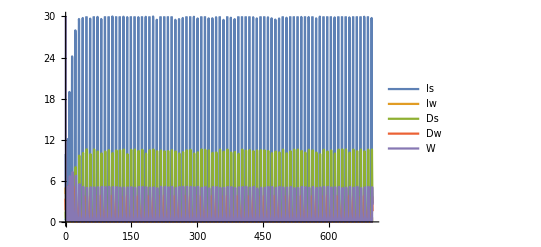

```mathematica
Plot[Evaluate[vart/.ndsol0Func1], {t, 0, maxt}, PlotRange-> {{0, maxt}, {0, 30}}, PlotLegends->{"Is", "Iw", "Ds","Dw", "W"}]
```

## Mutant dynamics

```mathematica
dImudt = γm M Is  - (d + α)Imu -(Ds+Dw) (ρ+βm)Imu; (*Infected intermediate*)
dDmdt = Imu βm Ds - (μ + σ)Dm;
dMdt = fm Dm - δ M - γm Is M;
```

```mathematica
dMdt > 0
```

Dm fm-Is M γm-M δ>0

```mathematica
Am = {{-d-α - (Ds+Dw) (ρ+βm), 0, γm Is},{βm Ds, -μ -σ, 0},{0, fm, -δ- γm Is}};
Am//MatrixForm
```

(-d-α-(Ds+Dw) (βm+ρ) | 0 | Is γm
Ds βm | -μ-σ | 0
0 | fm | -Is γm-δ)

```mathematica
Am.{Imu, Dm, M} == {dImudt, dDmdt, dMdt}//FullSimplify
```

True

```mathematica
FMat = {{0, 0, 0},{0, 0, 0}, {0, fm, 0}};
```

```mathematica
VMat ={{d+α+(Ds+Dw) (ρ+βm), 0, - Is γm},{-Ds βm, μ + σ, 0}, {0, 0, Is γm + δ}};
```

```mathematica
FMat - VMat == Am//FullSimplify
FMat-VMat//MatrixForm
```

True

(-d-α-(Ds+Dw) (βm+ρ) | 0 | Is γm
Ds βm | -μ-σ | 0
0 | fm | -Is γm-δ)

```mathematica
R0 = Eigenvalues[FMat.Inverse[VMat]][[3]]//FullSimplify
```

(Ds fm Is βm γm)/((Is γm+δ) (d+α+(Ds+Dw) (βm+ρ)) (μ+σ))

R0=fm/(Is γm+δ)(Is  γm)/(d+α+(Ds+Dw) (ρ+βm))(Ds  βm)/(μ+σ)

# Double infection

## Resident and mutant dynamics

Assumptions:
1. Fixed number of total intermediate hosts and definitive hosts
2. An infinite parasite pool such that reproduction of parasite does not affect the dynamics of the pool
3. We track the frequency dynamics of four compartments instead of density dynamics: Iw: intermediate host infected with a wild type, Iww: intermediate host infected with two wild types, Dw: definitive host infected with a wild type, Dww: definitive host infected with two wild type.
Is: frequency of susceptible intermediate host (1 - Iw - Iww)
Ds: frequency of susceptible definitive host (1 - Dw - Dww)
p: probability that two parasites make it into the intermediate host
q: probability that two parasites make it into the definitive host

```mathematica
dIwdt =  (1-m) ηS Is - (d + αw)Iw -Π[βw] Iw; 
dIwwdt =  (1-m)^2 ηC Is  - (d + αww)Iww -Π[βww] Iww;
dDwdt =(λS +1/2 λmix)Ds- (μ + σw) Dw -(λS + λSM + λmix)Dw;dDwwdt = λC Ds + (λS + 1/2 λmix) Dw - (μ + σww)Dww;
```

```mathematica
dImdt =  m ηS Is  - (d + αm)Imut - Π[βm]Imut;
dImwdt =2  m(1-m)ηC Is   - (d + αwm) Imw - Π[βmw] Imw;
dImmdt = m^2 ηC Is  - (d + αmm)Imm - Π[βmm]Imm;
dDmdt = (λSM +1/2 λmix)Ds - (μ + σm)Dw - (λSM + λS + λmix)Dm;
dDmwdt = λCmix Ds + (λS +1/2 λmix)Dm + (λSM + 1/2λmix) Dw- (μ + σmw) Dmw;
dDmmdt = λCM Ds +(λSM+1/2λmix) Dm - (μ + σmm) Dmm;
```

```mathematica
condFixTotal = {Is -> (1 - Iw - Iww), Ds -> (1 - Dw - Dww)};
Π[x_] := (b0 +x);
ηS = (1-p)γ
ηC = p γ
λS= βw Iw + (1-q)βww Iww;
λC = q βww Iww;
λSM = βm Imut + (1-q)βmm Imm;
λmix =  (1-q) βmw Imw;
λCmix = q βmw Imw;
λCM = q βmm Imm;
```

(1-p) γ

p γ

## Analysing the resident dynamics

Equilibrium

```mathematica
condResOnly = {m-> 0,Imut-> 0,  Imm-> 0, Imw -> 0};
```

```mathematica
solsres = Solve[{dIwdt == 0, dIwwdt == 0, dDwdt == 0, dDwwdt == 0}/.condFixTotal/.condResOnly, {Iw, Iww, Dw, Dww}];
```

```mathematica
Iw/.solsres;
Reduce[%≥ 0 && γ > 0 && b0 > 0 && d > 0 && αww >0 && βww > 0 && 0≤ p≤1 && αw > 0 && 0≤ q≤ 1, Reals]//FullSimplify
```

0≤q≤1&&βww>0&&αww>0&&d>0&&b0>0&&αw>0&&γ>0&&((p==1&&b0+d+αw+βw≠0)||((b0+d+αww+βww+p γ) ((b0+d+αw+βw) (b0+d+αww+βww)+(b0+d+αww+p (αw-αww+βw-βww)+βww) γ)>0&&0≤p<1))

```mathematica
1/(b0+d+αww+βww+p γ)(-b0^2-2 b0 d-d^2-b0 αw-d αw-b0 αww-d αww-αw αww-b0 βww-d βww-αw βww-b0 γ-d γ-p αw γ-αww γ+p αww γ-βww γ+p βww γ)//FullSimplify
```

-(((b0+d+αw) (b0+d+αww+βww)+(b0+d+αww+p (αw-αww-βww)+βww) γ)/(b0+d+αww+βww+p γ))

-((b0+d+αw) (b0+d+αww+βww)+(b0+d+αww+βww)γ+p (αw-αww-βww) γ)/(b0+d+αww+βww+p γ)
-((b0+d+αw) (b0+d+αww+βww)+(b0+d+αww+βww)γ+p (αw-αww-βww) γ)/(b0+d+αww+βww+p γ)
-((b0+d+αw + γ) (b0+d+αww+βww)+p (αw-αww-βww) γ)/(b0+d+αww+βww+p γ)
-((b0+d+αw ) (b0+d+αww+βww)+ γ (b0+d)+p  γ αw + γ(αww+βww)(1-p))/(b0+d+αww+βww+p γ)

```mathematica
-(((b0+d+αw ) (b0+d+αww+βww)+ γ (b0+d)+p  γ αw + γ(αww+βww)(1-p) )/(b0+d+αww+βww+p γ))== 1/(b0+d+αww+βww+p γ)(-b0^2-2 b0 d-d^2-b0 αw-d αw-b0 αww-d αww-αw αww-b0 βww-d βww-αw βww-b0 γ-d γ-p αw γ-αww γ+p αww γ-βww γ+p βww γ)//FullSimplify
```

True

```mathematica
Iww/.solsres;
Reduce[% > 0 && αw > 0 && 0≤ p ≤ 1 && βw > 0 && d > 0 && b0 > 0 && γ > 0 && αww > 0 , βww,Reals]
```

βw>0&&αw>0&&d>0&&b0>0&&0<p≤1&&γ>0&&αww>0&&βww>(-b0^2-2 b0 d-d^2-b0 αw-d αw-b0 αww-d αww-αw αww-b0 βw-d βw-αww βw-b0 γ-d γ-p αw γ-αww γ+p αww γ-p βw γ)/(b0+d+αw+βw+γ-p γ)

```mathematica
1/(b0+d+αw+βw+γ-p γ)(-b0^2-2 b0 d-d^2-b0 αw-d αw-b0 αww-d αww-αw αww-b0 βw-d βw-αww βw-b0 γ-d γ-p αw γ-αww γ+p αww γ-p βw γ)//FullSimplify
```

-((b0+d+αww) (b0+d+αw+βw)+(b0+d+αww+p (αw-αww+βw)) γ)/(b0+d+αw+βw+γ-p γ)

-((b0+d+αww) (b0+d+αw+βw)+(b0+d+αww+p (αw-αww+βw)) γ)/(b0+d+αw+βw+γ-p γ)
-((b0+d+αww) (b0+d+αw+βw + γ)+p (αw-αww+βw)γ)/(b0+d+αw+βw+γ(1-p))
-((b0+d+αww) (b0+d+αw+βw) + γ(b0+d)+(αw+βw)p γ+ αww γ(1- p ))/(b0+d+αw+βw+γ(1-p))

```mathematica
Dressols = Solve[{dDwdt == 0, dDwwdt == 0}/.condFixTotal/.condResOnly, {Dw, Dww}]//FullSimplify;
```

```mathematica
Reduce[(Dw/.Dressols) > 0 && μ > 0 && Iw > 0 && Iww > 0 && 0<q<1 && σw>0 && σww > 0&& βw > 0 && βww > 0, {Iw, Iww}]//Simplify
```

σww>0&&σw>0&&μ>0&&0<q<1&&βww>0&&βw>0&&Iw>0&&Iww>0

```mathematica
Reduce[(Dww/.Dressols) > 0 && μ > 0 && Iw > 0 && Iww > 0 && 0<q<1 && σw>0 && σww > 0&& βw > 0 && βww > 0, {Iw, Iww}]//Simplify
```

σww>0&&σw>0&&μ>0&&0<q<1&&βww>0&&βw>0&&Iw>0&&Iww>0

Equilibrium stability conditions

```mathematica
JRes = D[{dIwdt, dIwwdt, dDwdt, dDwwdt}/.condFixTotal/.condResOnly, {{Iw, Iww, Dw, Dww}}]//Simplify
```

{{-b0-d-αw-βw-γ+p γ,(-1+p) γ,0,0},{-p γ,-b0-d-αww-βww-p γ,0,0},{-(-1+2 Dw+Dww) βw,(-1+2 Dw+Dww) (-1+q) βww,-2 Iw βw+2 Iww (-1+q) βww-μ-σw,-Iw βw+Iww (-1+q) βww},{Dw βw,(Dw+q-2 Dw q-Dww q) βww,Iw βw+Iww (1-2 q) βww,-Iww q βww-μ-σww}}

```mathematica
JRes//MatrixForm
```

(-b0-d-αw-βw-γ+p γ | (-1+p) γ | 0 | 0
-p γ | -b0-d-αww-βww-p γ | 0 | 0
-(-1+2 Dw+Dww) βw | (-1+2 Dw+Dww) (-1+q) βww | -2 Iw βw+2 Iww (-1+q) βww-μ-σw | -Iw βw+Iww (-1+q) βww
Dw βw | (Dw+q-2 Dw q-Dww q) βww | Iw βw+Iww (1-2 q) βww | -Iww q βww-μ-σww)

```mathematica
eigvals = Eigenvalues[JRes]//FullSimplify
```

{1/2 (-2 b0-2 d-αw-αww-βw-βww-γ-√((αw-αww+βw-βww)^2-2 (-1+2 p) (αw-αww+βw-βww) γ+γ^2)),1/2 (-2 b0-2 d-αw-αww-βw-βww-γ+√((αw-αww+βw-βww)^2-2 (-1+2 p) (αw-αww+βw-βww) γ+γ^2)),1/2 (-2 Iw βw+Iww (-2+q) βww-2 μ-σw-√(Iww^2 q^2 βww^2-2 Iww (-2+3 q) βww (σw-σww)+(σw-σww) (4 Iw βw+σw-σww))-σww),1/2 (-2 Iw βw+Iww (-2+q) βww-2 μ-σw+√(Iww^2 q^2 βww^2-2 Iww (-2+3 q) βww (σw-σww)+(σw-σww) (4 Iw βw+σw-σww))-σww)}

Check with function Reduce

```mathematica
Reduce[eigvals[[2]]<0&& 1>p>0&& d > 0&&βw>0&&βww >0 && αw > 0&& αww > 0&& b0 > 0&& γ >0]
```

βww>0&&αww>0&&βw>0&&αw>0&&γ>0&&d>0&&b0>0&&0<p<1

Check with some algebra

```mathematica
eigvals[[2]]
```

1/2 (-2 b0-2 d-αw-αww-βw-βww-γ+√((αw-αww+βw-βww)^2-2 (-1+2 p) (αw-αww+βw-βww) γ+γ^2))

1/2 (-2 b0-2 d-αw-αww-βw-βww-γ+√((αw-αww+βw-βww)^2-2 (-1+2 p) (αw-αww+βw-βww) γ+γ^2))
If p = 0:
(αw-αww+βw-βww)^2-2 (-1+2 p) (αw-αww+βw-βww) γ+γ^2 = (αw-αww+βw-βww)^2+2  (αw-αww+βw-βww) γ+γ^2 = (αw-αww+βw-βww + γ)^2

The whole expression become
1/2 (-2 b0-2 d-αw-αww-βw-βww-γ+|αw-αww+βw-βww + γ|) < 0 in all cases

If p = 1:
(αw-αww+βw-βww)^2-2 (-1+2 p) (αw-αww+βw-βww) γ+γ^2 = (αw-αww+βw-βww)^2-2  (αw-αww+βw-βww) γ+γ^2 = (αw-αww+βw-βww - γ)^2
The whole expression become
1/2 (-2 b0-2 d-αw-αww-βw-βww-γ+|αw-αww+βw-βww - γ|) < 0 in all cases

The eigenvalue cannot be imaginary because the part under the square root is always positive

```mathematica
Reduce[(αw-αww+βw-βww + γ)^2-4 p(αw-αww+βw-βww) γ < 0 && αww >0 && αw > 0&& βw > 0 && βww > 0 && 0<p<1 && γ > 0]
```

False

```mathematica
eigvals[[4]]
```

1/2 (-2 Iw βw+Iww (-2+q) βww-2 μ-σw+√(Iww^2 q^2 βww^2-2 Iww (-2+3 q) βww (σw-σww)+(σw-σww) (4 Iw βw+σw-σww))-σww)

Check with function Reduce [Still there are some doubts]

```mathematica
Reduce[eigvals[[4]]>0&& 1>q>0&& d > 0&&βw>0&&βww >0 && σw > 0&& σww > 0&& Iww > 0&& Iw >0 && μ > 0]
```

False

Check with some algebra

If q = 0

1/2 (-2 Iw βw-2 Iww βww-2 μ-σw+√((σw-σww) (4 Iw βw+4 Iww βww+σw-σww))-σww)

1/2 (-2 Iw βw-2 Iww βww-2 μ-σw+√((σw-σww) (4 Iw βw+4 Iww βww+σw-σww))-σww)<0
iff 
2 Iw βw+2 Iww βww+2 μ+σw+σww>√((σw-σww) (4 Iw βw+4 Iww βww+σw-σww))
iff
(2 Iw βw+2 Iww βww+2 μ+σw+σww)^2>(σw-σww) (4 Iw βw+4 Iww βww+σw-σww)
iff
4 (Iw^2 βw^2+Iww^2 βww^2+2 Iww βww (μ+σww)+(μ+σw) (μ+σww)+2 Iw βw (Iww βww+μ+σww))) > 0  in all cases

Using some functions to simplify some expression above

```mathematica
Expand[(2 Iw βw+2 Iww βww+2 μ+σw+σww)^2]-Expand[(σw-σww) (4 Iw βw+4 Iww βww+σw-σww)]//FullSimplify
```

4 (Iw^2 βw^2+Iww^2 βww^2+2 Iww βww (μ+σww)+(μ+σw) (μ+σww)+2 Iw βw (Iww βww+μ+σww))

```mathematica
1/2 (-2 Iw βw+Iww (-2+q) βww-2 μ-σw+√(Iww^2 q^2 βww^2-2 Iww (-2+3 q) βww (σw-σww)+(σw-σww) (4 Iw βw+σw-σww))-σww)/.q-> 0//FullSimplify
```

1/2 (-2 Iw βw-2 Iww βww-2 μ-σw+√((σw-σww) (4 Iw βw+4 Iww βww+σw-σww))-σww)

If q = 1
1/2 (-2 Iw βw-Iww βww-2 μ-σw-σww+√(4 Iw βw (σw-σww)+(Iww βww-σw+σww)^2))

1/2 (-2 Iw βw-Iww βww-2 μ-σw-σww+√(4 Iw βw (σw-σww)+(Iww βww-σw+σww)^2))< 0
iff 
2 Iw βw+Iww βww+2 μ+σw+σww>√(4 Iw βw (σw-σww)+(Iww βww-σw+σww)^2)
iff
(2 Iw βw+Iww βww+2 μ+σw+σww)^2>4 Iw βw (σw-σww)+(Iww βww-σw+σww)^2
iff
4 (Iw^2 βw^2+(μ+σw) (Iww βww+μ+σww)+Iw βw (Iww βww+2 (μ+σww)))>0 True in all cases

```mathematica
1/2 (-2 Iw βw+Iww (-2+q) βww-2 μ-σw+√(Iww^2 q^2 βww^2-2 Iww (-2+3 q) βww (σw-σww)+(σw-σww) (4 Iw βw+σw-σww))-σww)/.q-> 1//FullSimplify
```

1/2 (-2 Iw βw-Iww βww-2 μ-σw-σww+√(4 Iw βw (σw-σww)+(Iww βww-σw+σww)^2))

```mathematica
Expand[(2 Iw βw+Iww βww+2 μ+σw+σww)^2]-4 Iw βw (σw-σww)-Expand[(Iww βww-σw+σww)^2]//Simplify
```

4 (Iw^2 βw^2+(μ+σw) (Iww βww+μ+σww)+Iw βw (Iww βww+2 (μ+σww)))

Check if the part under the square root is negative (i.e. potential for imaginary eigenvalue)

```mathematica
ToExpression[Import["/Users/Linh-phuong/resstability.txt"]];
```

```mathematica
(*(Iww^2 q^2 βww^2-2 Iww (-2+3 q) βww (σw-σww)+(σw-σww) (4 Iw βw+σw-σww))/.Iw -> FullSimplify[Iw/.solsres]/.Iww -> FullSimplify[Iww/.solsres]//FullSimplify
AbsoluteTiming[Reduce[%>0 &&1>p>0 && 1>q>0&& d > 0&&βw>0&&βww >0 && σw > 0&& σww > 0&& αww > 0&& αw >0&&γ > 0 && b0 > 0]//Simplify]*)
```

Summarise conditions for positive part under the square root

0<p≤(βw (b0+d+αww+βww))/((b0+d+αww) βw+(b0+d+αw+2 βw) βww) && 0<σww<X1
|| σww > X2

(βw (b0+d+αww+βww))/((b0+d+αww) βw+(b0+d+αw+2 βw) βww)<p<1 &&0<q<(-(-1+p) (b0+d+αww) βw+(p (b0+d+αw)+βw) βww)/(2 p (b0+d+αw+βw) βww)&&&& 0<σww<X1
|| σww > X2

(βw (b0+d+αww+βww))/((b0+d+αww) βw+(b0+d+αw+2 βw) βww)<p<1 && q==(-(-1+p) (b0+d+αww) βw+(p (b0+d+αw)+βw) βww)/(2 p (b0+d+αw+βw) βww) && σww  ≠ X2


(βw (b0+d+αww+βww))/((b0+d+αww) βw+(b0+d+αw+2 βw) βww)<p<1  &&(-(-1+p) (b0+d+αww) βw+(p (b0+d+αw)+βw) βww)/(2 p (b0+d+αw+βw) βww)<q<1 


X1 = -2 √((((-1+p) (b0+d+αww) βw+(p (-1+q) (b0+d+αw)+(-1+p q) βw) βww) ((-1+p) (b0+d+αww) βw+(p (-1+2 q) (b0+d+αw)+(-1+2 p q) βw) βww) γ^2)/((b0+d+αw+βw) (b0+d+αww+βww)+(b0+d+αww+p (αw-αww+βw-βww)+βww) γ)^2)+((-2 (-1+p) (b0+d+αww) βw+(-p (-2+3 q) (b0+d+αw)+(2-3 p q) βw) βww) γ+((b0+d+αw+βw) (b0+d+αww+βww)+(b0+d+αww+p (αw-αww+βw-βww)+βww) γ) σw)/((b0+d+αw+βw) (b0+d+αww+βww)+(b0+d+αww+p (αw-αww+βw-βww)+βww) γ) 
X2 = 2 √((((-1+p) (b0+d+αww) βw+(p (-1+q) (b0+d+αw)+(-1+p q) βw) βww) ((-1+p) (b0+d+αww) βw+(p (-1+2 q) (b0+d+αw)+(-1+2 p q) βw) βww) γ^2)/((b0+d+αw+βw) (b0+d+αww+βww)+(b0+d+αww+p (αw-αww+βw-βww)+βww) γ)^2)+((-2 (-1+p) (b0+d+αww) βw+(-p (-2+3 q) (b0+d+αw)+(2-3 p q) βw) βww) γ+((b0+d+αw+βw) (b0+d+αww+βww)+(b0+d+αww+p (αw-αww+βw-βww)+βww) γ) σw)/((b0+d+αw+βw) (b0+d+αww+βww)+(b0+d+αww+p (αw-αww+βw-βww)+βww) γ)

Threshold values

```mathematica
pthreshold = (βw (b0+d+αww+βww))/((b0+d+αww) βw+(b0+d+αw+2 βw) βww);
qthreshold = (-(-1+p) (b0+d+αww) βw+(p (b0+d+αw)+βw) βww)/(2 p (b0+d+αw+βw) βww);
σwwthreshold1 = -2 √((((-1+p) (b0+d+αww) βw+(p (-1+q) (b0+d+αw)+(-1+p q) βw) βww) ((-1+p) (b0+d+αww) βw+(p (-1+2 q) (b0+d+αw)+(-1+2 p q) βw) βww) γ^2)/((b0+d+αw+βw) (b0+d+αww+βww)+(b0+d+αww+p (αw-αww+βw-βww)+βww) γ)^2)+((-2 (-1+p) (b0+d+αww) βw+(-p (-2+3 q) (b0+d+αw)+(2-3 p q) βw) βww) γ+((b0+d+αw+βw) (b0+d+αww+βww)+(b0+d+αww+p (αw-αww+βw-βww)+βww) γ) σw)/((b0+d+αw+βw) (b0+d+αww+βww)+(b0+d+αww+p (αw-αww+βw-βww)+βww) γ) ;
σwwthreshold2 =  2 √((((-1+p) (b0+d+αww) βw+(p (-1+q) (b0+d+αw)+(-1+p q) βw) βww) ((-1+p) (b0+d+αww) βw+(p (-1+2 q) (b0+d+αw)+(-1+2 p q) βw) βww) γ^2)/((b0+d+αw+βw) (b0+d+αww+βww)+(b0+d+αww+p (αw-αww+βw-βww)+βww) γ)^2)+((-2 (-1+p) (b0+d+αww) βw+(-p (-2+3 q) (b0+d+αw)+(2-3 p q) βw) βww) γ+((b0+d+αw+βw) (b0+d+αww+βww)+(b0+d+αww+p (αw-αww+βw-βww)+βww) γ) σw)/((b0+d+αw+βw) (b0+d+αww+βww)+(b0+d+αww+p (αw-αww+βw-βww)+βww) γ)
```

2 √((((-1+p) (b0+d+αww) βw+(p (-1+q) (b0+d+αw)+(-1+p q) βw) βww) ((-1+p) (b0+d+αww) βw+(p (-1+2 q) (b0+d+αw)+(-1+2 p q) βw) βww) γ^2)/((b0+d+αw+βw) (b0+d+αww+βww)+(b0+d+αww+p (αw-αww+βw-βww)+βww) γ)^2)+((-2 (-1+p) (b0+d+αww) βw+(-p (-2+3 q) (b0+d+αw)+(2-3 p q) βw) βww) γ+((b0+d+αw+βw) (b0+d+αww+βww)+(b0+d+αww+p (αw-αww+βw-βww)+βww) γ) σw)/((b0+d+αw+βw) (b0+d+αww+βww)+(b0+d+αww+p (αw-αww+βw-βww)+βww) γ)

```mathematica
-2 Iw βw+Iww (-2+q) βww-2 μ-σw-σww/.Iw-> FullSimplify[Iw/.solsres]/.Iww-> FullSimplify[Iww/.solsres]//FullSimplify
Reduce[% < 0 && 0<p<1 && b0 > 0 && d > 0 && μ > 0 && αw > 0 &&αww > 0 && γ > 0 && 0<q<1 && βw > 0 && βww > 0 && σww > 0  && σw>0]//Simplify
```

{{((2 (-1+p) (b0+d+αww) βw+(p (-2+q) (b0+d+αw)+(-2+p q) βw) βww) γ)/((b0+d+αw+βw) (b0+d+αww+βww)+(b0+d+αww+p (αw-αww+βw-βww)+βww) γ)-2 μ-σw-σww}}

b0>0&&d>0&&0<p<1&&0<q<1&&αw>0&&αww>0&&βw>0&&βww>0&&γ>0&&μ>0&&σw>0&&σww>0

Numerical analysis

```mathematica
resvar = {Iw, Iww, Dw, Dww};
resvart = {Iw[t], Iww[t], Dw[t], Dww[t]};
{dIwdt, dIwwdt, dDwdt, dDwwdt}/.condResOnly/.condFixTotal/.Thread[resvar-> resvart];
ressys = Thread[D[resvart, t]==%];
```

### No differences in manipulation and virulence between single infection and double infections

```mathematica
qthreshold/.βww -> βw/.αww -> αw//FullSimplify
```

1/(2 p)

```mathematica
pareco1 = {b0 -> 1.3, γ -> 4.2, p -> 0.15, q -> 0.12, d -> 1.4, μ-> 1.2, αw -> 0.4, αww -> 0.4, βw -> 0.5, βww-> 0.5, σw -> 0.6, σww -> 0.45};
```

```mathematica
tmax =  10;
init = {Iw[0] == 0.2, Iww[0] ==  0.1, Dw[0] == 0.4, Dww[0] == 0.1};
```

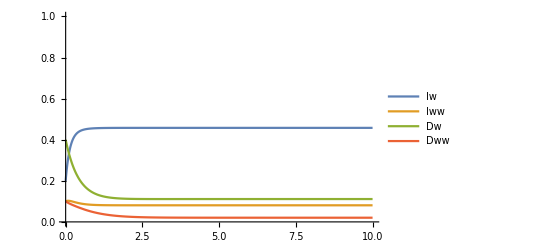

```mathematica
NDSolve[Join[{ressys, init}]/.pareco1, {Iw, Iww, Dw, Dww}, {t, 0, tmax}];
Plot[Evaluate[resvart/.%],{t, 0, tmax}, PlotRange->{{0, tmax} , {0, 1}}, PlotLegends->{"Iw", "Iww", "Dw", "Dww"}]
```

### Only similarity in virulence between single infection and double infections

```mathematica
qthreshold/.{αw -> α, αww -> α}//FullSimplify;
Reduce[0<% < 1 && b0 > 0 && d > 0 && α > 0 && 1>p>0 && βw > 0 && βww > 0, βww]//FullSimplify
```

α>0&&d>0&&b0>0&&βw>0&&βw/(b0+d+α+2 βw)<p<1&&βww>-((-1+p) (b0+d+α) βw)/(-βw+p (b0+d+α+2 βw))

```mathematica
pareco2 = {b0 -> 1.3, γ -> 4.2, p -> 0.15, q -> 0.12, d -> 1.4, μ-> 1.2, αw -> 0.4, αww -> 0.4, βw -> 0.5, βww-> 1.5, σw -> 0.6, σww -> 0.45};
```

```mathematica
{pthreshold<p<1}/.pareco2
q <qthreshold/.pareco2
0<σww<σwwthreshold1/.pareco2
```

{False}

True

True

```mathematica
tmax =  10;
init = {Iw[0] == 0.2, Iww[0] ==  0.1, Dw[0] == 0.4, Dww[0] == 0.1};
```

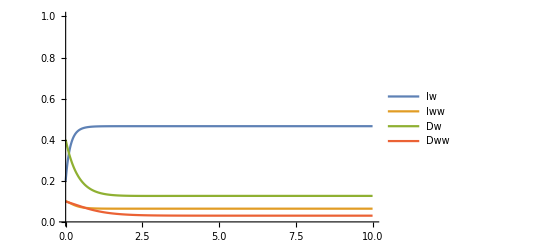

```mathematica
NDSolve[Join[{ressys, init}]/.pareco2, {Iw, Iww, Dw, Dww}, {t, 0, tmax}];
Plot[Evaluate[resvart/.%],{t, 0, tmax}, PlotRange->{{0, tmax} , {0, 1}}, PlotLegends->{"Iw", "Iww", "Dw", "Dww"}]
```

```mathematica
pareco3 = {b0 -> 1.3, γ -> 4.2, p -> 0.15, q -> 0.12, d -> 1.4, μ-> 1.2, αw -> 0.4, αww -> 0.4, βw -> 0.5, βww-> 12, σw -> 0.6, σww -> 1.9};
```

```mathematica
{pthreshold<p<1}/.pareco3
q <qthreshold/.pareco3
σww>σwwthreshold2/.pareco3
```

{True}

True

False

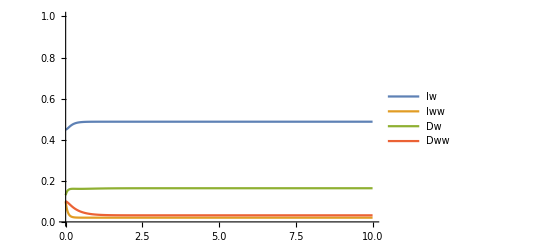

```mathematica
tmax =  10;
init = {Iw[0] == 0.45, Iww[0] ==  0.1, Dw[0] == 0.13, Dww[0] == 0.1};
NDSolve[Join[{ressys, init}]/.pareco3, {Iw, Iww, Dw, Dww}, {t, 0, tmax}];
Plot[Evaluate[resvart/.%],{t, 0, tmax}, PlotRange->{{0, tmax} , {0, 1}}, PlotLegends->{"Iw", "Iww", "Dw", "Dww"}]
```

```mathematica
parecobeta =  {b0 -> 1.3, γ -> 4.2, p -> 0.15, q -> 0.12, d -> 1.4, μ-> 1.2, αw -> 0.4, αww -> 0.4, βw -> 0.5, σw -> 0.45, σww -> 0.45};
```

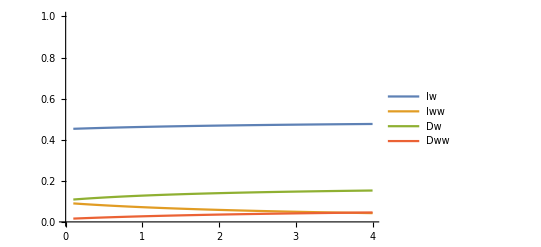

```mathematica
Plot[{Iw/.solsres/.parecobeta, Iww/.solsres/.parecobeta, Dw/.solsres/.parecobeta, Dww/.solsres/.parecobeta}, {βww, 0.1, 4}, PlotRange->{{0, 4}, {0, 1}}, PlotLegends->{"Iw", "Iww", "Dw", "Dww"}]
```

## Dynamics of both mutant and resident

```mathematica
simplifyCond = {αw -> α, αww-> α, αwm-> α, αm-> α, αmm-> α, σw-> σ, σww-> σ, σwm-> σ, σmm-> σ, βww-> β, βw -> β, βmw -> β, βmm -> β,βm -> β};
```

```mathematica
posCondSimple = {α > 0 && σ > 0 && β > 0 &&1> m > 0 && 1>p>0 && b0>0 && d > 0 && γ > 0 &&μ > 0 && 1>q>0};
```

```mathematica
solgenSim =Solve[{dIwdt == 0, dIwwdt == 0, dDwdt==0, dDwwdt==0, dImdt == 0, dImwdt ==0, dImmdt==0, dDmdt == 0, dDmwdt==0, dDmmdt == 0}/.condFixTotal/.simplifyCond, {Iw, Iww, Dw, Dww, Imut, Imw, Imm, Dm, Dmw, Dmm}];
```

```mathematica
Iw/.solgenSim//FullSimplify
```

{((-1+m) (-1+p) γ)/(b0+d+α+β+(-1+m) (-1+m p) γ)}

```mathematica
Iww/.solgenSim//FullSimplify
```

{((-1+m)^2 p γ)/(b0+d+α+β+(-1+m) (-1+m p) γ)}

```mathematica
Imut/.solgenSim//FullSimplify
```

{-(m (-1+p) γ)/(b0+d+α+β+(-1+m) (-1+m p) γ)}

```mathematica
Imw/.solgenSim//FullSimplify
```

{-(2 (-1+m) m p γ)/(b0+d+α+β+(-1+m) (-1+m p) γ)}

```mathematica
Imm/.solgenSim//FullSimplify
```

{(m^2 p γ)/(b0+d+α+β+(-1+m) (-1+m p) γ)}

```mathematica
Dw/.solgenSim//FullSimplify
```

{((-1+m) (-1+p q) β γ (b0+d+α+β+(-1+m) (-1+m p) γ) (μ+σ))/((b0+d+α+(-1+m) (-1+m p) γ)^2 (μ+σ)^2+β (b0+d+α+(-1+m) (-1+m p) γ) (μ+σ) ((2-m+(-1+(-1+m) m) p q) γ+2 (μ+σ))+β^2 (-(-1+m)^2 (-1+p q) γ^2+(2-m+(-1+(-1+m) m) p q) γ (μ+σ)+(μ+σ)^2))}

```mathematica
Dww/.solgenSim//FullSimplify
```

{((-1+m)^2 β γ (p q (b0+d+α+(-1+m) (-1+m p) γ) (μ+σ)+β (γ-p q γ+p q (μ+σ))))/((b0+d+α+(-1+m) (-1+m p) γ)^2 (μ+σ)^2+β (b0+d+α+(-1+m) (-1+m p) γ) (μ+σ) ((2-m+(-1+(-1+m) m) p q) γ+2 (μ+σ))+β^2 (-(-1+m)^2 (-1+p q) γ^2+(2-m+(-1+(-1+m) m) p q) γ (μ+σ)+(μ+σ)^2))}

```mathematica
JFull = D[{dIwdt, dIwwdt, dDwdt, dDwwdt, dImdt, dImmdt, dImwdt, dDmdt, dDmwdt, dDmmdt}/.condFixTotal/.simplifyCond, {{Iw, Iww, Dw, Dww, Imut, Imm, Imw, Dm, Dmw, Dmm}}]//Simplify;
eigvalFull = Eigenvalues[JFull]//FullSimplify
```

{-((Imm+Imut+Imw+Iw+Iww-(Imm+Imw+Iww) q) β),-b0-d-α-β,-b0-d-α-β,-b0-d-α-β,-b0-d-α-β,-b0-d-α-β-(-1+m) (-1+m p) γ,1/4 (-((2 Imm+2 Imut+3 Imw+4 (Iw+Iww)-(2 Imm+3 Imw+2 Iww) q+√((2 Imut+Imw) (2 Imut+5 Imw+8 (Iw+Iww))+4 Imm^2 (-1+q)^2-2 (6 Imut (Imw+2 Iww)+Imw (5 Imw+4 Iw+10 Iww)) q+(Imw+2 Iww) (5 Imw+2 Iww) q^2-4 Imm (-1+q) (2 Imut+3 Imw+4 (Iw+Iww)-3 (Imw+2 Iww) q))) β)-4 (μ+σ)),1/4 ((-2 Imut-4 (Iw+Iww)+2 Imm (-1+q)+3 Imw (-1+q)+2 Iww q) β+√((2 Imut+Imw) (2 Imut+5 Imw+8 (Iw+Iww))+4 Imm^2 (-1+q)^2-2 (6 Imut (Imw+2 Iww)+Imw (5 Imw+4 Iw+10 Iww)) q+(Imw+2 Iww) (5 Imw+2 Iww) q^2-4 Imm (-1+q) (2 Imut+3 Imw+4 (Iw+Iww)-3 (Imw+2 Iww) q)) β-4 (μ+σ)),-μ-σ,-μ-σmw}

```mathematica
eigvalFull[[8]]/.solgenSim//FullSimplify
```

{1/2 (β √((((4-3 m) m-2 m (5+(-5+m) m) p q+(1+m-m^2)^2 p^2 q^2) γ^2)/(b0+d+α+β+(-1+m) (-1+m p) γ)^2)+((-2+m+p q+m p (q-m q)) β γ)/(b0+d+α+β+(-1+m) (-1+m p) γ)-2 μ-2 σ)}

```mathematica
And@@{eigvalFull[[8]]>0 && Imut > 0 && Iww > 0 && Imm > 0 && Imw > 0 , posCondSimple[[1]]};
```

(α>0&&0<m<1&&0<p<1&&b0>0&&d>0&&γ>0&&Imm>0&&Imw>0&&0<Iww<-2 Imm-Imw+1/2 √5 √(4 Imm^2+4 Imm Imw+Imw^2)&&0<Imut<-2 Iww+√5 √(Iww^2)&&(4 Imm+4 Imut+2 Imw)/(4 Imm+2 Imw+Iww)<q≤(4 Imm^2+4 Imm Imut+4 Imm Imw+2 Imut Imw+Imw^2-8 Imm Iww-8 Imut Iww-4 Imw Iww)/(4 Imm^2+4 Imm Imw+Imw^2-16 Imm Iww-8 Imw Iww-4 Iww^2)-2 √5 √((4 Imm^2 Iww^2+8 Imm Imut Iww^2+4 Imut^2 Iww^2+4 Imm Imw Iww^2+4 Imut Imw Iww^2+Imw^2 Iww^2)/((4 Imm^2+4 Imm Imw+Imw^2-16 Imm Iww-8 Imw Iww-4 Iww^2)^2))&&1/2 (-Imw-2 Iww+Imw q+Iww q)-1/2 √(-4 Imm Iww q-4 Imut Iww q-2 Imw Iww q+4 Imm Iww q^2+2 Imw Iww q^2+Iww^2 q^2)<Iw<1/2 (-Imw-2 Iww+Imw q+Iww q)+1/2 √(-4 Imm Iww q-4 Imut Iww q-2 Imw Iww q+4 Imm Iww q^2+2 Imw Iww q^2+Iww^2 q^2)&&μ>0&&σ>0&&β>(-2 Imm μ-2 Imut μ-3 Imw μ-4 Iw μ-4 Iww μ+2 Imm q μ+3 Imw q μ+2 Iww q μ-2 Imm σ-2 Imut σ-3 Imw σ-4 Iw σ-4 Iww σ+2 Imm q σ+3 Imw q σ+2 Iww q σ)/(Imw^2+4 Imw Iw+4 Iw^2+4 Imw Iww+8 Iw Iww+4 Iww^2-2 Imw^2 q-4 Imw Iw q+4 Imm Iww q+4 Imut Iww q-4 Imw Iww q-4 Iw Iww q-4 Iww^2 q+Imw^2 q^2-4 Imm Iww q^2)+√((4 Imm^2 μ^2+8 Imm Imut μ^2+4 Imut^2 μ^2+12 Imm Imw μ^2+12 Imut Imw μ^2+5 Imw^2 μ^2+16 Imm Iw μ^2+16 Imut Iw μ^2+8 Imw Iw μ^2+16 Imm Iww μ^2+16 Imut Iww μ^2+8 Imw Iww μ^2-8 Imm^2 q μ^2-8 Imm Imut q μ^2-24 Imm Imw q μ^2-12 Imut Imw q μ^2-10 Imw^2 q μ^2-16 Imm Iw q μ^2-8 Imw Iw q μ^2-40 Imm Iww q μ^2-24 Imut Iww q μ^2-20 Imw Iww q μ^2+4 Imm^2 q^2 μ^2+12 Imm Imw q^2 μ^2+5 Imw^2 q^2 μ^2+24 Imm Iww q^2 μ^2+12 Imw Iww q^2 μ^2+4 Iww^2 q^2 μ^2+8 Imm^2 μ σ+16 Imm Imut μ σ+8 Imut^2 μ σ+24 Imm Imw μ σ+24 Imut Imw μ σ+10 Imw^2 μ σ+32 Imm Iw μ σ+32 Imut Iw μ σ+16 Imw Iw μ σ+32 Imm Iww μ σ+32 Imut Iww μ σ+16 Imw Iww μ σ-16 Imm^2 q μ σ-16 Imm Imut q μ σ-48 Imm Imw q μ σ-24 Imut Imw q μ σ-20 Imw^2 q μ σ-32 Imm Iw q μ σ-16 Imw Iw q μ σ-80 Imm Iww q μ σ-48 Imut Iww q μ σ-40 Imw Iww q μ σ+8 Imm^2 q^2 μ σ+24 Imm Imw q^2 μ σ+10 Imw^2 q^2 μ σ+48 Imm Iww q^2 μ σ+24 Imw Iww q^2 μ σ+8 Iww^2 q^2 μ σ+4 Imm^2 σ^2+8 Imm Imut σ^2+4 Imut^2 σ^2+12 Imm Imw σ^2+12 Imut Imw σ^2+5 Imw^2 σ^2+16 Imm Iw σ^2+16 Imut Iw σ^2+8 Imw Iw σ^2+16 Imm Iww σ^2+16 Imut Iww σ^2+8 Imw Iww σ^2-8 Imm^2 q σ^2-8 Imm Imut q σ^2-24 Imm Imw q σ^2-12 Imut Imw q σ^2-10 Imw^2 q σ^2-16 Imm Iw q σ^2-8 Imw Iw q σ^2-40 Imm Iww q σ^2-24 Imut Iww q σ^2-20 Imw Iww q σ^2+4 Imm^2 q^2 σ^2+12 Imm Imw q^2 σ^2+5 Imw^2 q^2 σ^2+24 Imm Iww q^2 σ^2+12 Imw Iww q^2 σ^2+4 Iww^2 q^2 σ^2)/(Imw^2+4 Imw Iw+4 Iw^2+4 Imw Iww+8 Iw Iww+4 Iww^2-2 Imw^2 q-4 Imw Iw q+4 Imm Iww q+4 Imut Iww q-4 Imw Iww q-4 Iw Iww q-4 Iww^2 q+Imw^2 q^2-4 Imm Iww q^2)^2))||(α>0&&0<m<1&&0<p<1&&b0>0&&d>0&&γ>0&&Imm>0&&Imw>0&&0<Iww<-2 Imm-Imw+1/2 √5 √(4 Imm^2+4 Imm Imw+Imw^2)&&0<Imut<-2 Iww+√5 √(Iww^2)&&(4 Imm^2+4 Imm Imut+4 Imm Imw+2 Imut Imw+Imw^2-8 Imm Iww-8 Imut Iww-4 Imw Iww)/(4 Imm^2+4 Imm Imw+Imw^2-16 Imm Iww-8 Imw Iww-4 Iww^2)-2 √5 √((4 Imm^2 Iww^2+8 Imm Imut Iww^2+4 Imut^2 Iww^2+4 Imm Imw Iww^2+4 Imut Imw Iww^2+Imw^2 Iww^2)/((4 Imm^2+4 Imm Imw+Imw^2-16 Imm Iww-8 Imw Iww-4 Iww^2)^2))<q<1&&(4 Imm^2+8 Imm Imut+4 Imut^2+12 Imm Imw+12 Imut Imw+5 Imw^2+16 Imm Iww+16 Imut Iww+8 Imw Iww-8 Imm^2 q-8 Imm Imut q-24 Imm Imw q-12 Imut Imw q-10 Imw^2 q-40 Imm Iww q-24 Imut Iww q-20 Imw Iww q+4 Imm^2 q^2+12 Imm Imw q^2+5 Imw^2 q^2+24 Imm Iww q^2+12 Imw Iww q^2+4 Iww^2 q^2)/(-16 Imm-16 Imut-8 Imw+16 Imm q+8 Imw q)<Iw<1/2 (-Imw-2 Iww+Imw q+Iww q)-1/2 √(-4 Imm Iww q-4 Imut Iww q-2 Imw Iww q+4 Imm Iww q^2+2 Imw Iww q^2+Iww^2 q^2)&&μ>0&&σ>0&&(-2 Imm μ-2 Imut μ-3 Imw μ-4 Iw μ-4 Iww μ+2 Imm q μ+3 Imw q μ+2 Iww q μ-2 Imm σ-2 Imut σ-3 Imw σ-4 Iw σ-4 Iww σ+2 Imm q σ+3 Imw q σ+2 Iww q σ)/(Imw^2+4 Imw Iw+4 Iw^2+4 Imw Iww+8 Iw Iww+4 Iww^2-2 Imw^2 q-4 Imw Iw q+4 Imm Iww q+4 Imut Iww q-4 Imw Iww q-4 Iw Iww q-4 Iww^2 q+Imw^2 q^2-4 Imm Iww q^2)-√((4 Imm^2 μ^2+8 Imm Imut μ^2+4 Imut^2 μ^2+12 Imm Imw μ^2+12 Imut Imw μ^2+5 Imw^2 μ^2+16 Imm Iw μ^2+16 Imut Iw μ^2+8 Imw Iw μ^2+16 Imm Iww μ^2+16 Imut Iww μ^2+8 Imw Iww μ^2-8 Imm^2 q μ^2-8 Imm Imut q μ^2-24 Imm Imw q μ^2-12 Imut Imw q μ^2-10 Imw^2 q μ^2-16 Imm Iw q μ^2-8 Imw Iw q μ^2-40 Imm Iww q μ^2-24 Imut Iww q μ^2-20 Imw Iww q μ^2+4 Imm^2 q^2 μ^2+12 Imm Imw q^2 μ^2+5 Imw^2 q^2 μ^2+24 Imm Iww q^2 μ^2+12 Imw Iww q^2 μ^2+4 Iww^2 q^2 μ^2+8 Imm^2 μ σ+16 Imm Imut μ σ+8 Imut^2 μ σ+24 Imm Imw μ σ+24 Imut Imw μ σ+10 Imw^2 μ σ+32 Imm Iw μ σ+32 Imut Iw μ σ+16 Imw Iw μ σ+32 Imm Iww μ σ+32 Imut Iww μ σ+16 Imw Iww μ σ-16 Imm^2 q μ σ-16 Imm Imut q μ σ-48 Imm Imw q μ σ-24 Imut Imw q μ σ-20 Imw^2 q μ σ-32 Imm Iw q μ σ-16 Imw Iw q μ σ-80 Imm Iww q μ σ-48 Imut Iww q μ σ-40 Imw Iww q μ σ+8 Imm^2 q^2 μ σ+24 Imm Imw q^2 μ σ+10 Imw^2 q^2 μ σ+48 Imm Iww q^2 μ σ+24 Imw Iww q^2 μ σ+8 Iww^2 q^2 μ σ+4 Imm^2 σ^2+8 Imm Imut σ^2+4 Imut^2 σ^2+12 Imm Imw σ^2+12 Imut Imw σ^2+5 Imw^2 σ^2+16 Imm Iw σ^2+16 Imut Iw σ^2+8 Imw Iw σ^2+16 Imm Iww σ^2+16 Imut Iww σ^2+8 Imw Iww σ^2-8 Imm^2 q σ^2-8 Imm Imut q σ^2-24 Imm Imw q σ^2-12 Imut Imw q σ^2-10 Imw^2 q σ^2-16 Imm Iw q σ^2-8 Imw Iw q σ^2-40 Imm Iww q σ^2-24 Imut Iww q σ^2-20 Imw Iww q σ^2+4 Imm^2 q^2 σ^2+12 Imm Imw q^2 σ^2+5 Imw^2 q^2 σ^2+24 Imm Iww q^2 σ^2+12 Imw Iww q^2 σ^2+4 Iww^2 q^2 σ^2)/(Imw^2+4 Imw Iw+4 Iw^2+4 Imw Iww+8 Iw Iww+4 Iww^2-2 Imw^2 q-4 Imw Iw q+4 Imm Iww q+4 Imut Iww q-4 Imw Iww q-4 Iw Iww q-4 Iww^2 q+Imw^2 q^2-4 Imm Iww q^2)^2)<β≤(4 μ+4 σ)/(-2 Imm-2 Imut-3 Imw-4 Iw-4 Iww+2 Imm q+3 Imw q+2 Iww q))||(α>0&&0<m<1&&0<p<1&&b0>0&&d>0&&γ>0&&Imm>0&&Imw>0&&0<Iww<-2 Imm-Imw+1/2 √5 √(4 Imm^2+4 Imm Imw+Imw^2)&&0<Imut<-2 Iww+√5 √(Iww^2)&&(4 Imm^2+4 Imm Imut+4 Imm Imw+2 Imut Imw+Imw^2-8 Imm Iww-8 Imut Iww-4 Imw Iww)/(4 Imm^2+4 Imm Imw+Imw^2-16 Imm Iww-8 Imw Iww-4 Iww^2)-2 √5 √((4 Imm^2 Iww^2+8 Imm Imut Iww^2+4 Imut^2 Iww^2+4 Imm Imw Iww^2+4 Imut Imw Iww^2+Imw^2 Iww^2)/((4 Imm^2+4 Imm Imw+Imw^2-16 Imm Iww-8 Imw Iww-4 Iww^2)^2))<q<1&&Iw==1/2 (-Imw-2 Iww+Imw q+Iww q)-1/2 √(-4 Imm Iww q-4 Imut Iww q-2 Imw Iww q+4 Imm Iww q^2+2 Imw Iww q^2+Iww^2 q^2)&&μ>0&&σ>0&&(2 μ+2 σ)/(-2 Imm-2 Imut-3 Imw-4 Iw-4 Iww+2 Imm q+3 Imw q+2 Iww q)<β≤(4 μ+4 σ)/(-2 Imm-2 Imut-3 Imw-4 Iw-4 Iww+2 Imm q+3 Imw q+2 Iww q))||(α>0&&0<m<1&&0<p<1&&b0>0&&d>0&&γ>0&&Imm>0&&Imw>0&&0<Iww<-2 Imm-Imw+1/2 √5 √(4 Imm^2+4 Imm Imw+Imw^2)&&0<Imut<-2 Iww+√5 √(Iww^2)&&(4 Imm^2+4 Imm Imut+4 Imm Imw+2 Imut Imw+Imw^2-8 Imm Iww-8 Imut Iww-4 Imw Iww)/(4 Imm^2+4 Imm Imw+Imw^2-16 Imm Iww-8 Imw Iww-4 Iww^2)-2 √5 √((4 Imm^2 Iww^2+8 Imm Imut Iww^2+4 Imut^2 Iww^2+4 Imm Imw Iww^2+4 Imut Imw Iww^2+Imw^2 Iww^2)/((4 Imm^2+4 Imm Imw+Imw^2-16 Imm Iww-8 Imw Iww-4 Iww^2)^2))<q<1&&1/2 (-Imw-2 Iww+Imw q+Iww q)-1/2 √(-4 Imm Iww q-4 Imut Iww q-2 Imw Iww q+4 Imm Iww q^2+2 Imw Iww q^2+Iww^2 q^2)<Iw<1/4 (-2 Imm-2 Imut-3 Imw-4 Iww+2 Imm q+3 Imw q+2 Iww q)&&μ>0&&σ>0&&(-2 Imm μ-2 Imut μ-3 Imw μ-4 Iw μ-4 Iww μ+2 Imm q μ+3 Imw q μ+2 Iww q μ-2 Imm σ-2 Imut σ-3 Imw σ-4 Iw σ-4 Iww σ+2 Imm q σ+3 Imw q σ+2 Iww q σ)/(Imw^2+4 Imw Iw+4 Iw^2+4 Imw Iww+8 Iw Iww+4 Iww^2-2 Imw^2 q-4 Imw Iw q+4 Imm Iww q+4 Imut Iww q-4 Imw Iww q-4 Iw Iww q-4 Iww^2 q+Imw^2 q^2-4 Imm Iww q^2)+√((4 Imm^2 μ^2+8 Imm Imut μ^2+4 Imut^2 μ^2+12 Imm Imw μ^2+12 Imut Imw μ^2+5 Imw^2 μ^2+16 Imm Iw μ^2+16 Imut Iw μ^2+8 Imw Iw μ^2+16 Imm Iww μ^2+16 Imut Iww μ^2+8 Imw Iww μ^2-8 Imm^2 q μ^2-8 Imm Imut q μ^2-24 Imm Imw q μ^2-12 Imut Imw q μ^2-10 Imw^2 q μ^2-16 Imm Iw q μ^2-8 Imw Iw q μ^2-40 Imm Iww q μ^2-24 Imut Iww q μ^2-20 Imw Iww q μ^2+4 Imm^2 q^2 μ^2+12 Imm Imw q^2 μ^2+5 Imw^2 q^2 μ^2+24 Imm Iww q^2 μ^2+12 Imw Iww q^2 μ^2+4 Iww^2 q^2 μ^2+8 Imm^2 μ σ+16 Imm Imut μ σ+8 Imut^2 μ σ+24 Imm Imw μ σ+24 Imut Imw μ σ+10 Imw^2 μ σ+32 Imm Iw μ σ+32 Imut Iw μ σ+16 Imw Iw μ σ+32 Imm Iww μ σ+32 Imut Iww μ σ+16 Imw Iww μ σ-16 Imm^2 q μ σ-16 Imm Imut q μ σ-48 Imm Imw q μ σ-24 Imut Imw q μ σ-20 Imw^2 q μ σ-32 Imm Iw q μ σ-16 Imw Iw q μ σ-80 Imm Iww q μ σ-48 Imut Iww q μ σ-40 Imw Iww q μ σ+8 Imm^2 q^2 μ σ+24 Imm Imw q^2 μ σ+10 Imw^2 q^2 μ σ+48 Imm Iww q^2 μ σ+24 Imw Iww q^2 μ σ+8 Iww^2 q^2 μ σ+4 Imm^2 σ^2+8 Imm Imut σ^2+4 Imut^2 σ^2+12 Imm Imw σ^2+12 Imut Imw σ^2+5 Imw^2 σ^2+16 Imm Iw σ^2+16 Imut Iw σ^2+8 Imw Iw σ^2+16 Imm Iww σ^2+16 Imut Iww σ^2+8 Imw Iww σ^2-8 Imm^2 q σ^2-8 Imm Imut q σ^2-24 Imm Imw q σ^2-12 Imut Imw q σ^2-10 Imw^2 q σ^2-16 Imm Iw q σ^2-8 Imw Iw q σ^2-40 Imm Iww q σ^2-24 Imut Iww q σ^2-20 Imw Iww q σ^2+4 Imm^2 q^2 σ^2+12 Imm Imw q^2 σ^2+5 Imw^2 q^2 σ^2+24 Imm Iww q^2 σ^2+12 Imw Iww q^2 σ^2+4 Iww^2 q^2 σ^2)/(Imw^2+4 Imw Iw+4 Iw^2+4 Imw Iww+8 Iw Iww+4 Iww^2-2 Imw^2 q-4 Imw Iw q+4 Imm Iww q+4 Imut Iww q-4 Imw Iww q-4 Iw Iww q-4 Iww^2 q+Imw^2 q^2-4 Imm Iww q^2)^2)<β≤(4 μ+4 σ)/(-2 Imm-2 Imut-3 Imw-4 Iw-4 Iww+2 Imm q+3 Imw q+2 Iww q))||(α>0&&0<m<1&&0<p<1&&b0>0&&d>0&&γ>0&&Imm>0&&Imw>0&&0<Iww<-2 Imm-Imw+1/2 √5 √(4 Imm^2+4 Imm Imw+Imw^2)&&0<Imut<-2 Iww+√5 √(Iww^2)&&(4 Imm^2+4 Imm Imut+4 Imm Imw+2 Imut Imw+Imw^2-8 Imm Iww-8 Imut Iww-4 Imw Iww)/(4 Imm^2+4 Imm Imw+Imw^2-16 Imm Iww-8 Imw Iww-4 Iww^2)-2 √5 √((4 Imm^2 Iww^2+8 Imm Imut Iww^2+4 Imut^2 Iww^2+4 Imm Imw Iww^2+4 Imut Imw Iww^2+Imw^2 Iww^2)/((4 Imm^2+4 Imm Imw+Imw^2-16 Imm Iww-8 Imw Iww-4 Iww^2)^2))<q<1&&1/4 (-2 Imm-2 Imut-3 Imw-4 Iww+2 Imm q+3 Imw q+2 Iww q)≤Iw<1/2 (-Imw-2 Iww+Imw q+Iww q)+1/2 √(-4 Imm Iww q-4 Imut Iww q-2 Imw Iww q+4 Imm Iww q^2+2 Imw Iww q^2+Iww^2 q^2)&&μ>0&&σ>0&&β>(-2 Imm μ-2 Imut μ-3 Imw μ-4 Iw μ-4 Iww μ+2 Imm q μ+3 Imw q μ+2 Iww q μ-2 Imm σ-2 Imut σ-3 Imw σ-4 Iw σ-4 Iww σ+2 Imm q σ+3 Imw q σ+2 Iww q σ)/(Imw^2+4 Imw Iw+4 Iw^2+4 Imw Iww+8 Iw Iww+4 Iww^2-2 Imw^2 q-4 Imw Iw q+4 Imm Iww q+4 Imut Iww q-4 Imw Iww q-4 Iw Iww q-4 Iww^2 q+Imw^2 q^2-4 Imm Iww q^2)+√((4 Imm^2 μ^2+8 Imm Imut μ^2+4 Imut^2 μ^2+12 Imm Imw μ^2+12 Imut Imw μ^2+5 Imw^2 μ^2+16 Imm Iw μ^2+16 Imut Iw μ^2+8 Imw Iw μ^2+16 Imm Iww μ^2+16 Imut Iww μ^2+8 Imw Iww μ^2-8 Imm^2 q μ^2-8 Imm Imut q μ^2-24 Imm Imw q μ^2-12 Imut Imw q μ^2-10 Imw^2 q μ^2-16 Imm Iw q μ^2-8 Imw Iw q μ^2-40 Imm Iww q μ^2-24 Imut Iww q μ^2-20 Imw Iww q μ^2+4 Imm^2 q^2 μ^2+12 Imm Imw q^2 μ^2+5 Imw^2 q^2 μ^2+24 Imm Iww q^2 μ^2+12 Imw Iww q^2 μ^2+4 Iww^2 q^2 μ^2+8 Imm^2 μ σ+16 Imm Imut μ σ+8 Imut^2 μ σ+24 Imm Imw μ σ+24 Imut Imw μ σ+10 Imw^2 μ σ+32 Imm Iw μ σ+32 Imut Iw μ σ+16 Imw Iw μ σ+32 Imm Iww μ σ+32 Imut Iww μ σ+16 Imw Iww μ σ-16 Imm^2 q μ σ-16 Imm Imut q μ σ-48 Imm Imw q μ σ-24 Imut Imw q μ σ-20 Imw^2 q μ σ-32 Imm Iw q μ σ-16 Imw Iw q μ σ-80 Imm Iww q μ σ-48 Imut Iww q μ σ-40 Imw Iww q μ σ+8 Imm^2 q^2 μ σ+24 Imm Imw q^2 μ σ+10 Imw^2 q^2 μ σ+48 Imm Iww q^2 μ σ+24 Imw Iww q^2 μ σ+8 Iww^2 q^2 μ σ+4 Imm^2 σ^2+8 Imm Imut σ^2+4 Imut^2 σ^2+12 Imm Imw σ^2+12 Imut Imw σ^2+5 Imw^2 σ^2+16 Imm Iw σ^2+16 Imut Iw σ^2+8 Imw Iw σ^2+16 Imm Iww σ^2+16 Imut Iww σ^2+8 Imw Iww σ^2-8 Imm^2 q σ^2-8 Imm Imut q σ^2-24 Imm Imw q σ^2-12 Imut Imw q σ^2-10 Imw^2 q σ^2-16 Imm Iw q σ^2-8 Imw Iw q σ^2-40 Imm Iww q σ^2-24 Imut Iww q σ^2-20 Imw Iww q σ^2+4 Imm^2 q^2 σ^2+12 Imm Imw q^2 σ^2+5 Imw^2 q^2 σ^2+24 Imm Iww q^2 σ^2+12 Imw Iww q^2 σ^2+4 Iww^2 q^2 σ^2)/(Imw^2+4 Imw Iw+4 Iw^2+4 Imw Iww+8 Iw Iww+4 Iww^2-2 Imw^2 q-4 Imw Iw q+4 Imm Iww q+4 Imut Iww q-4 Imw Iww q-4 Iw Iww q-4 Iww^2 q+Imw^2 q^2-4 Imm Iww q^2)^2))||(α>0&&0<m<1&&0<p<1&&b0>0&&d>0&&γ>0&&Imm>0&&Imw>0&&0<Iww<-2 Imm-Imw+1/2 √5 √(4 Imm^2+4 Imm Imw+Imw^2)&&0<Imut<-2 Iww+√5 √(Iww^2)&&(4 Imm^2+4 Imm Imut+4 Imm Imw+2 Imut Imw+Imw^2-8 Imm Iww-8 Imut Iww-4 Imw Iww)/(4 Imm^2+4 Imm Imw+Imw^2-16 Imm Iww-8 Imw Iww-4 Iww^2)-2 √5 √((4 Imm^2 Iww^2+8 Imm Imut Iww^2+4 Imut^2 Iww^2+4 Imm Imw Iww^2+4 Imut Imw Iww^2+Imw^2 Iww^2)/((4 Imm^2+4 Imm Imw+Imw^2-16 Imm Iww-8 Imw Iww-4 Iww^2)^2))<q<1&&(4 Imm^2+8 Imm Imut+4 Imut^2+12 Imm Imw+12 Imut Imw+5 Imw^2+16 Imm Iww+16 Imut Iww+8 Imw Iww-8 Imm^2 q-8 Imm Imut q-24 Imm Imw q-12 Imut Imw q-10 Imw^2 q-40 Imm Iww q-24 Imut Iww q-20 Imw Iww q+4 Imm^2 q^2+12 Imm Imw q^2+5 Imw^2 q^2+24 Imm Iww q^2+12 Imw Iww q^2+4 Iww^2 q^2)/(-16 Imm-16 Imut-8 Imw+16 Imm q+8 Imw q)≤Iw<1/4 (-2 Imm-2 Imut-3 Imw-4 Iww+2 Imm q+3 Imw q+2 Iww q)&&μ>0&&σ>0&&β>(4 μ+4 σ)/(-2 Imm-2 Imut-3 Imw-4 Iw-4 Iww+2 Imm q+3 Imw q+2 Iww q))||(α>0&&0<m<1&&0<p<1&&b0>0&&d>0&&γ>0&&Imm>0&&Imw>0&&0<Iww<-2 Imm-Imw+1/2 √5 √(4 Imm^2+4 Imm Imw+Imw^2)&&-2 Iww+√5 √(Iww^2)≤Imut<Iww/4&&(4 Imm+4 Imut+2 Imw)/(4 Imm+2 Imw+Iww)<q<1&&1/2 (-Imw-2 Iww+Imw q+Iww q)-1/2 √(-4 Imm Iww q-4 Imut Iww q-2 Imw Iww q+4 Imm Iww q^2+2 Imw Iww q^2+Iww^2 q^2)<Iw<1/2 (-Imw-2 Iww+Imw q+Iww q)+1/2 √(-4 Imm Iww q-4 Imut Iww q-2 Imw Iww q+4 Imm Iww q^2+2 Imw Iww q^2+Iww^2 q^2)&&μ>0&&σ>0&&β>(-2 Imm μ-2 Imut μ-3 Imw μ-4 Iw μ-4 Iww μ+2 Imm q μ+3 Imw q μ+2 Iww q μ-2 Imm σ-2 Imut σ-3 Imw σ-4 Iw σ-4 Iww σ+2 Imm q σ+3 Imw q σ+2 Iww q σ)/(Imw^2+4 Imw Iw+4 Iw^2+4 Imw Iww+8 Iw Iww+4 Iww^2-2 Imw^2 q-4 Imw Iw q+4 Imm Iww q+4 Imut Iww q-4 Imw Iww q-4 Iw Iww q-4 Iww^2 q+Imw^2 q^2-4 Imm Iww q^2)+√((4 Imm^2 μ^2+8 Imm Imut μ^2+4 Imut^2 μ^2+12 Imm Imw μ^2+12 Imut Imw μ^2+5 Imw^2 μ^2+16 Imm Iw μ^2+16 Imut Iw μ^2+8 Imw Iw μ^2+16 Imm Iww μ^2+16 Imut Iww μ^2+8 Imw Iww μ^2-8 Imm^2 q μ^2-8 Imm Imut q μ^2-24 Imm Imw q μ^2-12 Imut Imw q μ^2-10 Imw^2 q μ^2-16 Imm Iw q μ^2-8 Imw Iw q μ^2-40 Imm Iww q μ^2-24 Imut Iww q μ^2-20 Imw Iww q μ^2+4 Imm^2 q^2 μ^2+12 Imm Imw q^2 μ^2+5 Imw^2 q^2 μ^2+24 Imm Iww q^2 μ^2+12 Imw Iww q^2 μ^2+4 Iww^2 q^2 μ^2+8 Imm^2 μ σ+16 Imm Imut μ σ+8 Imut^2 μ σ+24 Imm Imw μ σ+24 Imut Imw μ σ+10 Imw^2 μ σ+32 Imm Iw μ σ+32 Imut Iw μ σ+16 Imw Iw μ σ+32 Imm Iww μ σ+32 Imut Iww μ σ+16 Imw Iww μ σ-16 Imm^2 q μ σ-16 Imm Imut q μ σ-48 Imm Imw q μ σ-24 Imut Imw q μ σ-20 Imw^2 q μ σ-32 Imm Iw q μ σ-16 Imw Iw q μ σ-80 Imm Iww q μ σ-48 Imut Iww q μ σ-40 Imw Iww q μ σ+8 Imm^2 q^2 μ σ+24 Imm Imw q^2 μ σ+10 Imw^2 q^2 μ σ+48 Imm Iww q^2 μ σ+24 Imw Iww q^2 μ σ+8 Iww^2 q^2 μ σ+4 Imm^2 σ^2+8 Imm Imut σ^2+4 Imut^2 σ^2+12 Imm Imw σ^2+12 Imut Imw σ^2+5 Imw^2 σ^2+16 Imm Iw σ^2+16 Imut Iw σ^2+8 Imw Iw σ^2+16 Imm Iww σ^2+16 Imut Iww σ^2+8 Imw Iww σ^2-8 Imm^2 q σ^2-8 Imm Imut q σ^2-24 Imm Imw q σ^2-12 Imut Imw q σ^2-10 Imw^2 q σ^2-16 Imm Iw q σ^2-8 Imw Iw q σ^2-40 Imm Iww q σ^2-24 Imut Iww q σ^2-20 Imw Iww q σ^2+4 Imm^2 q^2 σ^2+12 Imm Imw q^2 σ^2+5 Imw^2 q^2 σ^2+24 Imm Iww q^2 σ^2+12 Imw Iww q^2 σ^2+4 Iww^2 q^2 σ^2)/(Imw^2+4 Imw Iw+4 Iw^2+4 Imw Iww+8 Iw Iww+4 Iww^2-2 Imw^2 q-4 Imw Iw q+4 Imm Iww q+4 Imut Iww q-4 Imw Iww q-4 Iw Iww q-4 Iww^2 q+Imw^2 q^2-4 Imm Iww q^2)^2))||(α>0&&0<m<1&&0<p<1&&b0>0&&d>0&&γ>0&&Imm>0&&Imw>0&&Iww==-2 Imm-Imw+1/2 √5 √(4 Imm^2+4 Imm Imw+Imw^2)&&0<Imut<-2 Iww+√5 √(Iww^2)&&(4 Imm+4 Imut+2 Imw)/(4 Imm+2 Imw+Iww)<q<(2 Imm+2 Imut+Imw)/(4 Imm+2 Imw-8 Iww)&&1/2 (-Imw-2 Iww+Imw q+Iww q)-1/2 √(-4 Imm Iww q-4 Imut Iww q-2 Imw Iww q+4 Imm Iww q^2+2 Imw Iww q^2+Iww^2 q^2)<Iw<1/2 (-Imw-2 Iww+Imw q+Iww q)+1/2 √(-4 Imm Iww q-4 Imut Iww q-2 Imw Iww q+4 Imm Iww q^2+2 Imw Iww q^2+Iww^2 q^2)&&μ>0&&σ>0&&β>(-2 Imm μ-2 Imut μ-3 Imw μ-4 Iw μ-4 Iww μ+2 Imm q μ+3 Imw q μ+2 Iww q μ-2 Imm σ-2 Imut σ-3 Imw σ-4 Iw σ-4 Iww σ+2 Imm q σ+3 Imw q σ+2 Iww q σ)/(Imw^2+4 Imw Iw+4 Iw^2+4 Imw Iww+8 Iw Iww+4 Iww^2-2 Imw^2 q-4 Imw Iw q+4 Imm Iww q+4 Imut Iww q-4 Imw Iww q-4 Iw Iww q-4 Iww^2 q+Imw^2 q^2-4 Imm Iww q^2)+√((4 Imm^2 μ^2+8 Imm Imut μ^2+4 Imut^2 μ^2+12 Imm Imw μ^2+12 Imut Imw μ^2+5 Imw^2 μ^2+16 Imm Iw μ^2+16 Imut Iw μ^2+8 Imw Iw μ^2+16 Imm Iww μ^2+16 Imut Iww μ^2+8 Imw Iww μ^2-8 Imm^2 q μ^2-8 Imm Imut q μ^2-24 Imm Imw q μ^2-12 Imut Imw q μ^2-10 Imw^2 q μ^2-16 Imm Iw q μ^2-8 Imw Iw q μ^2-40 Imm Iww q μ^2-24 Imut Iww q μ^2-20 Imw Iww q μ^2+4 Imm^2 q^2 μ^2+12 Imm Imw q^2 μ^2+5 Imw^2 q^2 μ^2+24 Imm Iww q^2 μ^2+12 Imw Iww q^2 μ^2+4 Iww^2 q^2 μ^2+8 Imm^2 μ σ+16 Imm Imut μ σ+8 Imut^2 μ σ+24 Imm Imw μ σ+24 Imut Imw μ σ+10 Imw^2 μ σ+32 Imm Iw μ σ+32 Imut Iw μ σ+16 Imw Iw μ σ+32 Imm Iww μ σ+32 Imut Iww μ σ+16 Imw Iww μ σ-16 Imm^2 q μ σ-16 Imm Imut q μ σ-48 Imm Imw q μ σ-24 Imut Imw q μ σ-20 Imw^2 q μ σ-32 Imm Iw q μ σ-16 Imw Iw q μ σ-80 Imm Iww q μ σ-48 Imut Iww q μ σ-40 Imw Iww q μ σ+8 Imm^2 q^2 μ σ+24 Imm Imw q^2 μ σ+10 Imw^2 q^2 μ σ+48 Imm Iww q^2 μ σ+24 Imw Iww q^2 μ σ+8 Iww^2 q^2 μ σ+4 Imm^2 σ^2+8 Imm Imut σ^2+4 Imut^2 σ^2+12 Imm Imw σ^2+12 Imut Imw σ^2+5 Imw^2 σ^2+16 Imm Iw σ^2+16 Imut Iw σ^2+8 Imw Iw σ^2+16 Imm Iww σ^2+16 Imut Iww σ^2+8 Imw Iww σ^2-8 Imm^2 q σ^2-8 Imm Imut q σ^2-24 Imm Imw q σ^2-12 Imut Imw q σ^2-10 Imw^2 q σ^2-16 Imm Iw q σ^2-8 Imw Iw q σ^2-40 Imm Iww q σ^2-24 Imut Iww q σ^2-20 Imw Iww q σ^2+4 Imm^2 q^2 σ^2+12 Imm Imw q^2 σ^2+5 Imw^2 q^2 σ^2+24 Imm Iww q^2 σ^2+12 Imw Iww q^2 σ^2+4 Iww^2 q^2 σ^2)/(Imw^2+4 Imw Iw+4 Iw^2+4 Imw Iww+8 Iw Iww+4 Iww^2-2 Imw^2 q-4 Imw Iw q+4 Imm Iww q+4 Imut Iww q-4 Imw Iww q-4 Iw Iww q-4 Iww^2 q+Imw^2 q^2-4 Imm Iww q^2)^2))||(α>0&&0<m<1&&0<p<1&&b0>0&&d>0&&γ>0&&Imm>0&&Imw>0&&Iww==-2 Imm-Imw+1/2 √5 √(4 Imm^2+4 Imm Imw+Imw^2)&&0<Imut<-2 Iww+√5 √(Iww^2)&&q==(2 Imm+2 Imut+Imw)/(4 Imm+2 Imw-8 Iww)&&1/4 (-2 Imm-2 Imut-3 Imw-4 Iww+2 Imm q+3 Imw q+2 Iww q)<Iw<1/2 (-Imw-2 Iww+Imw q+Iww q)+1/2 √(-4 Imm Iww q-4 Imut Iww q-2 Imw Iww q+4 Imm Iww q^2+2 Imw Iww q^2+Iww^2 q^2)&&μ>0&&σ>0&&β>(-2 Imm μ-2 Imut μ-3 Imw μ-4 Iw μ-4 Iww μ+2 Imm q μ+3 Imw q μ+2 Iww q μ-2 Imm σ-2 Imut σ-3 Imw σ-4 Iw σ-4 Iww σ+2 Imm q σ+3 Imw q σ+2 Iww q σ)/(Imw^2+4 Imw Iw+4 Iw^2+4 Imw Iww+8 Iw Iww+4 Iww^2-2 Imw^2 q-4 Imw Iw q+4 Imm Iww q+4 Imut Iww q-4 Imw Iww q-4 Iw Iww q-4 Iww^2 q+Imw^2 q^2-4 Imm Iww q^2)+√((4 Imm^2 μ^2+8 Imm Imut μ^2+4 Imut^2 μ^2+12 Imm Imw μ^2+12 Imut Imw μ^2+5 Imw^2 μ^2+16 Imm Iw μ^2+16 Imut Iw μ^2+8 Imw Iw μ^2+16 Imm Iww μ^2+16 Imut Iww μ^2+8 Imw Iww μ^2-8 Imm^2 q μ^2-8 Imm Imut q μ^2-24 Imm Imw q μ^2-12 Imut Imw q μ^2-10 Imw^2 q μ^2-16 Imm Iw q μ^2-8 Imw Iw q μ^2-40 Imm Iww q μ^2-24 Imut Iww q μ^2-20 Imw Iww q μ^2+4 Imm^2 q^2 μ^2+12 Imm Imw q^2 μ^2+5 Imw^2 q^2 μ^2+24 Imm Iww q^2 μ^2+12 Imw Iww q^2 μ^2+4 Iww^2 q^2 μ^2+8 Imm^2 μ σ+16 Imm Imut μ σ+8 Imut^2 μ σ+24 Imm Imw μ σ+24 Imut Imw μ σ+10 Imw^2 μ σ+32 Imm Iw μ σ+32 Imut Iw μ σ+16 Imw Iw μ σ+32 Imm Iww μ σ+32 Imut Iww μ σ+16 Imw Iww μ σ-16 Imm^2 q μ σ-16 Imm Imut q μ σ-48 Imm Imw q μ σ-24 Imut Imw q μ σ-20 Imw^2 q μ σ-32 Imm Iw q μ σ-16 Imw Iw q μ σ-80 Imm Iww q μ σ-48 Imut Iww q μ σ-40 Imw Iww q μ σ+8 Imm^2 q^2 μ σ+24 Imm Imw q^2 μ σ+10 Imw^2 q^2 μ σ+48 Imm Iww q^2 μ σ+24 Imw Iww q^2 μ σ+8 Iww^2 q^2 μ σ+4 Imm^2 σ^2+8 Imm Imut σ^2+4 Imut^2 σ^2+12 Imm Imw σ^2+12 Imut Imw σ^2+5 Imw^2 σ^2+16 Imm Iw σ^2+16 Imut Iw σ^2+8 Imw Iw σ^2+16 Imm Iww σ^2+16 Imut Iww σ^2+8 Imw Iww σ^2-8 Imm^2 q σ^2-8 Imm Imut q σ^2-24 Imm Imw q σ^2-12 Imut Imw q σ^2-10 Imw^2 q σ^2-16 Imm Iw q σ^2-8 Imw Iw q σ^2-40 Imm Iww q σ^2-24 Imut Iww q σ^2-20 Imw Iww q σ^2+4 Imm^2 q^2 σ^2+12 Imm Imw q^2 σ^2+5 Imw^2 q^2 σ^2+24 Imm Iww q^2 σ^2+12 Imw Iww q^2 σ^2+4 Iww^2 q^2 σ^2)/(Imw^2+4 Imw Iw+4 Iw^2+4 Imw Iww+8 Iw Iww+4 Iww^2-2 Imw^2 q-4 Imw Iw q+4 Imm Iww q+4 Imut Iww q-4 Imw Iww q-4 Iw Iww q-4 Iww^2 q+Imw^2 q^2-4 Imm Iww q^2)^2))||(α>0&&0<m<1&&0<p<1&&b0>0&&d>0&&γ>0&&Imm>0&&Imw>0&&Iww==-2 Imm-Imw+1/2 √5 √(4 Imm^2+4 Imm Imw+Imw^2)&&0<Imut<-2 Iww+√5 √(Iww^2)&&(2 Imm+2 Imut+Imw)/(4 Imm+2 Imw-8 Iww)<q<1&&(4 Imm^2+8 Imm Imut+4 Imut^2+12 Imm Imw+12 Imut Imw+5 Imw^2+16 Imm Iww+16 Imut Iww+8 Imw Iww-8 Imm^2 q-8 Imm Imut q-24 Imm Imw q-12 Imut Imw q-10 Imw^2 q-40 Imm Iww q-24 Imut Iww q-20 Imw Iww q+4 Imm^2 q^2+12 Imm Imw q^2+5 Imw^2 q^2+24 Imm Iww q^2+12 Imw Iww q^2+4 Iww^2 q^2)/(-16 Imm-16 Imut-8 Imw+16 Imm q+8 Imw q)<Iw<1/2 (-Imw-2 Iww+Imw q+Iww q)-1/2 √(-4 Imm Iww q-4 Imut Iww q-2 Imw Iww q+4 Imm Iww q^2+2 Imw Iww q^2+Iww^2 q^2)&&μ>0&&σ>0&&(-2 Imm μ-2 Imut μ-3 Imw μ-4 Iw μ-4 Iww μ+2 Imm q μ+3 Imw q μ+2 Iww q μ-2 Imm σ-2 Imut σ-3 Imw σ-4 Iw σ-4 Iww σ+2 Imm q σ+3 Imw q σ+2 Iww q σ)/(Imw^2+4 Imw Iw+4 Iw^2+4 Imw Iww+8 Iw Iww+4 Iww^2-2 Imw^2 q-4 Imw Iw q+4 Imm Iww q+4 Imut Iww q-4 Imw Iww q-4 Iw Iww q-4 Iww^2 q+Imw^2 q^2-4 Imm Iww q^2)-√((4 Imm^2 μ^2+8 Imm Imut μ^2+4 Imut^2 μ^2+12 Imm Imw μ^2+12 Imut Imw μ^2+5 Imw^2 μ^2+16 Imm Iw μ^2+16 Imut Iw μ^2+8 Imw Iw μ^2+16 Imm Iww μ^2+16 Imut Iww μ^2+8 Imw Iww μ^2-8 Imm^2 q μ^2-8 Imm Imut q μ^2-24 Imm Imw q μ^2-12 Imut Imw q μ^2-10 Imw^2 q μ^2-16 Imm Iw q μ^2-8 Imw Iw q μ^2-40 Imm Iww q μ^2-24 Imut Iww q μ^2-20 Imw Iww q μ^2+4 Imm^2 q^2 μ^2+12 Imm Imw q^2 μ^2+5 Imw^2 q^2 μ^2+24 Imm Iww q^2 μ^2+12 Imw Iww q^2 μ^2+4 Iww^2 q^2 μ^2+8 Imm^2 μ σ+16 Imm Imut μ σ+8 Imut^2 μ σ+24 Imm Imw μ σ+24 Imut Imw μ σ+10 Imw^2 μ σ+32 Imm Iw μ σ+32 Imut Iw μ σ+16 Imw Iw μ σ+32 Imm Iww μ σ+32 Imut Iww μ σ+16 Imw Iww μ σ-16 Imm^2 q μ σ-16 Imm Imut q μ σ-48 Imm Imw q μ σ-24 Imut Imw q μ σ-20 Imw^2 q μ σ-32 Imm Iw q μ σ-16 Imw Iw q μ σ-80 Imm Iww q μ σ-48 Imut Iww q μ σ-40 Imw Iww q μ σ+8 Imm^2 q^2 μ σ+24 Imm Imw q^2 μ σ+10 Imw^2 q^2 μ σ+48 Imm Iww q^2 μ σ+24 Imw Iww q^2 μ σ+8 Iww^2 q^2 μ σ+4 Imm^2 σ^2+8 Imm Imut σ^2+4 Imut^2 σ^2+12 Imm Imw σ^2+12 Imut Imw σ^2+5 Imw^2 σ^2+16 Imm Iw σ^2+16 Imut Iw σ^2+8 Imw Iw σ^2+16 Imm Iww σ^2+16 Imut Iww σ^2+8 Imw Iww σ^2-8 Imm^2 q σ^2-8 Imm Imut q σ^2-24 Imm Imw q σ^2-12 Imut Imw q σ^2-10 Imw^2 q σ^2-16 Imm Iw q σ^2-8 Imw Iw q σ^2-40 Imm Iww q σ^2-24 Imut Iww q σ^2-20 Imw Iww q σ^2+4 Imm^2 q^2 σ^2+12 Imm Imw q^2 σ^2+5 Imw^2 q^2 σ^2+24 Imm Iww q^2 σ^2+12 Imw Iww q^2 σ^2+4 Iww^2 q^2 σ^2)/(Imw^2+4 Imw Iw+4 Iw^2+4 Imw Iww+8 Iw Iww+4 Iww^2-2 Imw^2 q-4 Imw Iw q+4 Imm Iww q+4 Imut Iww q-4 Imw Iww q-4 Iw Iww q-4 Iww^2 q+Imw^2 q^2-4 Imm Iww q^2)^2)<β≤(4 μ+4 σ)/(-2 Imm-2 Imut-3 Imw-4 Iw-4 Iww+2 Imm q+3 Imw q+2 Iww q))||(α>0&&0<m<1&&0<p<1&&b0>0&&d>0&&γ>0&&Imm>0&&Imw>0&&Iww==-2 Imm-Imw+1/2 √5 √(4 Imm^2+4 Imm Imw+Imw^2)&&0<Imut<-2 Iww+√5 √(Iww^2)&&(2 Imm+2 Imut+Imw)/(4 Imm+2 Imw-8 Iww)<q<1&&Iw==1/2 (-Imw-2 Iww+Imw q+Iww q)-1/2 √(-4 Imm Iww q-4 Imut Iww q-2 Imw Iww q+4 Imm Iww q^2+2 Imw Iww q^2+Iww^2 q^2)&&μ>0&&σ>0&&(2 μ+2 σ)/(-2 Imm-2 Imut-3 Imw-4 Iw-4 Iww+2 Imm q+3 Imw q+2 Iww q)<β≤(4 μ+4 σ)/(-2 Imm-2 Imut-3 Imw-4 Iw-4 Iww+2 Imm q+3 Imw q+2 Iww q))||(α>0&&0<m<1&&0<p<1&&b0>0&&d>0&&γ>0&&Imm>0&&Imw>0&&Iww==-2 Imm-Imw+1/2 √5 √(4 Imm^2+4 Imm Imw+Imw^2)&&0<Imut<-2 Iww+√5 √(Iww^2)&&(2 Imm+2 Imut+Imw)/(4 Imm+2 Imw-8 Iww)<q<1&&1/2 (-Imw-2 Iww+Imw q+Iww q)-1/2 √(-4 Imm Iww q-4 Imut Iww q-2 Imw Iww q+4 Imm Iww q^2+2 Imw Iww q^2+Iww^2 q^2)<Iw<1/4 (-2 Imm-2 Imut-3 Imw-4 Iww+2 Imm q+3 Imw q+2 Iww q)&&μ>0&&σ>0&&(-2 Imm μ-2 Imut μ-3 Imw μ-4 Iw μ-4 Iww μ+2 Imm q μ+3 Imw q μ+2 Iww q μ-2 Imm σ-2 Imut σ-3 Imw σ-4 Iw σ-4 Iww σ+2 Imm q σ+3 Imw q σ+2 Iww q σ)/(Imw^2+4 Imw Iw+4 Iw^2+4 Imw Iww+8 Iw Iww+4 Iww^2-2 Imw^2 q-4 Imw Iw q+4 Imm Iww q+4 Imut Iww q-4 Imw Iww q-4 Iw Iww q-4 Iww^2 q+Imw^2 q^2-4 Imm Iww q^2)+√((4 Imm^2 μ^2+8 Imm Imut μ^2+4 Imut^2 μ^2+12 Imm Imw μ^2+12 Imut Imw μ^2+5 Imw^2 μ^2+16 Imm Iw μ^2+16 Imut Iw μ^2+8 Imw Iw μ^2+16 Imm Iww μ^2+16 Imut Iww μ^2+8 Imw Iww μ^2-8 Imm^2 q μ^2-8 Imm Imut q μ^2-24 Imm Imw q μ^2-12 Imut Imw q μ^2-10 Imw^2 q μ^2-16 Imm Iw q μ^2-8 Imw Iw q μ^2-40 Imm Iww q μ^2-24 Imut Iww q μ^2-20 Imw Iww q μ^2+4 Imm^2 q^2 μ^2+12 Imm Imw q^2 μ^2+5 Imw^2 q^2 μ^2+24 Imm Iww q^2 μ^2+12 Imw Iww q^2 μ^2+4 Iww^2 q^2 μ^2+8 Imm^2 μ σ+16 Imm Imut μ σ+8 Imut^2 μ σ+24 Imm Imw μ σ+24 Imut Imw μ σ+10 Imw^2 μ σ+32 Imm Iw μ σ+32 Imut Iw μ σ+16 Imw Iw μ σ+32 Imm Iww μ σ+32 Imut Iww μ σ+16 Imw Iww μ σ-16 Imm^2 q μ σ-16 Imm Imut q μ σ-48 Imm Imw q μ σ-24 Imut Imw q μ σ-20 Imw^2 q μ σ-32 Imm Iw q μ σ-16 Imw Iw q μ σ-80 Imm Iww q μ σ-48 Imut Iww q μ σ-40 Imw Iww q μ σ+8 Imm^2 q^2 μ σ+24 Imm Imw q^2 μ σ+10 Imw^2 q^2 μ σ+48 Imm Iww q^2 μ σ+24 Imw Iww q^2 μ σ+8 Iww^2 q^2 μ σ+4 Imm^2 σ^2+8 Imm Imut σ^2+4 Imut^2 σ^2+12 Imm Imw σ^2+12 Imut Imw σ^2+5 Imw^2 σ^2+16 Imm Iw σ^2+16 Imut Iw σ^2+8 Imw Iw σ^2+16 Imm Iww σ^2+16 Imut Iww σ^2+8 Imw Iww σ^2-8 Imm^2 q σ^2-8 Imm Imut q σ^2-24 Imm Imw q σ^2-12 Imut Imw q σ^2-10 Imw^2 q σ^2-16 Imm Iw q σ^2-8 Imw Iw q σ^2-40 Imm Iww q σ^2-24 Imut Iww q σ^2-20 Imw Iww q σ^2+4 Imm^2 q^2 σ^2+12 Imm Imw q^2 σ^2+5 Imw^2 q^2 σ^2+24 Imm Iww q^2 σ^2+12 Imw Iww q^2 σ^2+4 Iww^2 q^2 σ^2)/(Imw^2+4 Imw Iw+4 Iw^2+4 Imw Iww+8 Iw Iww+4 Iww^2-2 Imw^2 q-4 Imw Iw q+4 Imm Iww q+4 Imut Iww q-4 Imw Iww q-4 Iw Iww q-4 Iww^2 q+Imw^2 q^2-4 Imm Iww q^2)^2)<β≤(4 μ+4 σ)/(-2 Imm-2 Imut-3 Imw-4 Iw-4 Iww+2 Imm q+3 Imw q+2 Iww q))||(α>0&&0<m<1&&0<p<1&&b0>0&&d>0&&γ>0&&Imm>0&&Imw>0&&Iww==-2 Imm-Imw+1/2 √5 √(4 Imm^2+4 Imm Imw+Imw^2)&&0<Imut<-2 Iww+√5 √(Iww^2)&&(2 Imm+2 Imut+Imw)/(4 Imm+2 Imw-8 Iww)<q<1&&1/4 (-2 Imm-2 Imut-3 Imw-4 Iww+2 Imm q+3 Imw q+2 Iww q)≤Iw<1/2 (-Imw-2 Iww+Imw q+Iww q)+1/2 √(-4 Imm Iww q-4 Imut Iww q-2 Imw Iww q+4 Imm Iww q^2+2 Imw Iww q^2+Iww^2 q^2)&&μ>0&&σ>0&&β>(-2 Imm μ-2 Imut μ-3 Imw μ-4 Iw μ-4 Iww μ+2 Imm q μ+3 Imw q μ+2 Iww q μ-2 Imm σ-2 Imut σ-3 Imw σ-4 Iw σ-4 Iww σ+2 Imm q σ+3 Imw q σ+2 Iww q σ)/(Imw^2+4 Imw Iw+4 Iw^2+4 Imw Iww+8 Iw Iww+4 Iww^2-2 Imw^2 q-4 Imw Iw q+4 Imm Iww q+4 Imut Iww q-4 Imw Iww q-4 Iw Iww q-4 Iww^2 q+Imw^2 q^2-4 Imm Iww q^2)+√((4 Imm^2 μ^2+8 Imm Imut μ^2+4 Imut^2 μ^2+12 Imm Imw μ^2+12 Imut Imw μ^2+5 Imw^2 μ^2+16 Imm Iw μ^2+16 Imut Iw μ^2+8 Imw Iw μ^2+16 Imm Iww μ^2+16 Imut Iww μ^2+8 Imw Iww μ^2-8 Imm^2 q μ^2-8 Imm Imut q μ^2-24 Imm Imw q μ^2-12 Imut Imw q μ^2-10 Imw^2 q μ^2-16 Imm Iw q μ^2-8 Imw Iw q μ^2-40 Imm Iww q μ^2-24 Imut Iww q μ^2-20 Imw Iww q μ^2+4 Imm^2 q^2 μ^2+12 Imm Imw q^2 μ^2+5 Imw^2 q^2 μ^2+24 Imm Iww q^2 μ^2+12 Imw Iww q^2 μ^2+4 Iww^2 q^2 μ^2+8 Imm^2 μ σ+16 Imm Imut μ σ+8 Imut^2 μ σ+24 Imm Imw μ σ+24 Imut Imw μ σ+10 Imw^2 μ σ+32 Imm Iw μ σ+32 Imut Iw μ σ+16 Imw Iw μ σ+32 Imm Iww μ σ+32 Imut Iww μ σ+16 Imw Iww μ σ-16 Imm^2 q μ σ-16 Imm Imut q μ σ-48 Imm Imw q μ σ-24 Imut Imw q μ σ-20 Imw^2 q μ σ-32 Imm Iw q μ σ-16 Imw Iw q μ σ-80 Imm Iww q μ σ-48 Imut Iww q μ σ-40 Imw Iww q μ σ+8 Imm^2 q^2 μ σ+24 Imm Imw q^2 μ σ+10 Imw^2 q^2 μ σ+48 Imm Iww q^2 μ σ+24 Imw Iww q^2 μ σ+8 Iww^2 q^2 μ σ+4 Imm^2 σ^2+8 Imm Imut σ^2+4 Imut^2 σ^2+12 Imm Imw σ^2+12 Imut Imw σ^2+5 Imw^2 σ^2+16 Imm Iw σ^2+16 Imut Iw σ^2+8 Imw Iw σ^2+16 Imm Iww σ^2+16 Imut Iww σ^2+8 Imw Iww σ^2-8 Imm^2 q σ^2-8 Imm Imut q σ^2-24 Imm Imw q σ^2-12 Imut Imw q σ^2-10 Imw^2 q σ^2-16 Imm Iw q σ^2-8 Imw Iw q σ^2-40 Imm Iww q σ^2-24 Imut Iww q σ^2-20 Imw Iww q σ^2+4 Imm^2 q^2 σ^2+12 Imm Imw q^2 σ^2+5 Imw^2 q^2 σ^2+24 Imm Iww q^2 σ^2+12 Imw Iww q^2 σ^2+4 Iww^2 q^2 σ^2)/(Imw^2+4 Imw Iw+4 Iw^2+4 Imw Iww+8 Iw Iww+4 Iww^2-2 Imw^2 q-4 Imw Iw q+4 Imm Iww q+4 Imut Iww q-4 Imw Iww q-4 Iw Iww q-4 Iww^2 q+Imw^2 q^2-4 Imm Iww q^2)^2))||(α>0&&0<m<1&&0<p<1&&b0>0&&d>0&&γ>0&&Imm>0&&Imw>0&&Iww==-2 Imm-Imw+1/2 √5 √(4 Imm^2+4 Imm Imw+Imw^2)&&0<Imut<-2 Iww+√5 √(Iww^2)&&(2 Imm+2 Imut+Imw)/(4 Imm+2 Imw-8 Iww)<q<1&&(4 Imm^2+8 Imm Imut+4 Imut^2+12 Imm Imw+12 Imut Imw+5 Imw^2+16 Imm Iww+16 Imut Iww+8 Imw Iww-8 Imm^2 q-8 Imm Imut q-24 Imm Imw q-12 Imut Imw q-10 Imw^2 q-40 Imm Iww q-24 Imut Iww q-20 Imw Iww q+4 Imm^2 q^2+12 Imm Imw q^2+5 Imw^2 q^2+24 Imm Iww q^2+12 Imw Iww q^2+4 Iww^2 q^2)/(-16 Imm-16 Imut-8 Imw+16 Imm q+8 Imw q)≤Iw<1/4 (-2 Imm-2 Imut-3 Imw-4 Iww+2 Imm q+3 Imw q+2 Iww q)&&μ>0&&σ>0&&β>(4 μ+4 σ)/(-2 Imm-2 Imut-3 Imw-4 Iw-4 Iww+2 Imm q+3 Imw q+2 Iww q))||(α>0&&0<m<1&&0<p<1&&b0>0&&d>0&&γ>0&&Imm>0&&Imw>0&&Iww==-2 Imm-Imw+1/2 √5 √(4 Imm^2+4 Imm Imw+Imw^2)&&-2 Iww+√5 √(Iww^2)≤Imut<Iww/4&&(4 Imm+4 Imut+2 Imw)/(4 Imm+2 Imw+Iww)<q<1&&1/2 (-Imw-2 Iww+Imw q+Iww q)-1/2 √(-4 Imm Iww q-4 Imut Iww q-2 Imw Iww q+4 Imm Iww q^2+2 Imw Iww q^2+Iww^2 q^2)<Iw<1/2 (-Imw-2 Iww+Imw q+Iww q)+1/2 √(-4 Imm Iww q-4 Imut Iww q-2 Imw Iww q+4 Imm Iww q^2+2 Imw Iww q^2+Iww^2 q^2)&&μ>0&&σ>0&&β>(-2 Imm μ-2 Imut μ-3 Imw μ-4 Iw μ-4 Iww μ+2 Imm q μ+3 Imw q μ+2 Iww q μ-2 Imm σ-2 Imut σ-3 Imw σ-4 Iw σ-4 Iww σ+2 Imm q σ+3 Imw q σ+2 Iww q σ)/(Imw^2+4 Imw Iw+4 Iw^2+4 Imw Iww+8 Iw Iww+4 Iww^2-2 Imw^2 q-4 Imw Iw q+4 Imm Iww q+4 Imut Iww q-4 Imw Iww q-4 Iw Iww q-4 Iww^2 q+Imw^2 q^2-4 Imm Iww q^2)+√((4 Imm^2 μ^2+8 Imm Imut μ^2+4 Imut^2 μ^2+12 Imm Imw μ^2+12 Imut Imw μ^2+5 Imw^2 μ^2+16 Imm Iw μ^2+16 Imut Iw μ^2+8 Imw Iw μ^2+16 Imm Iww μ^2+16 Imut Iww μ^2+8 Imw Iww μ^2-8 Imm^2 q μ^2-8 Imm Imut q μ^2-24 Imm Imw q μ^2-12 Imut Imw q μ^2-10 Imw^2 q μ^2-16 Imm Iw q μ^2-8 Imw Iw q μ^2-40 Imm Iww q μ^2-24 Imut Iww q μ^2-20 Imw Iww q μ^2+4 Imm^2 q^2 μ^2+12 Imm Imw q^2 μ^2+5 Imw^2 q^2 μ^2+24 Imm Iww q^2 μ^2+12 Imw Iww q^2 μ^2+4 Iww^2 q^2 μ^2+8 Imm^2 μ σ+16 Imm Imut μ σ+8 Imut^2 μ σ+24 Imm Imw μ σ+24 Imut Imw μ σ+10 Imw^2 μ σ+32 Imm Iw μ σ+32 Imut Iw μ σ+16 Imw Iw μ σ+32 Imm Iww μ σ+32 Imut Iww μ σ+16 Imw Iww μ σ-16 Imm^2 q μ σ-16 Imm Imut q μ σ-48 Imm Imw q μ σ-24 Imut Imw q μ σ-20 Imw^2 q μ σ-32 Imm Iw q μ σ-16 Imw Iw q μ σ-80 Imm Iww q μ σ-48 Imut Iww q μ σ-40 Imw Iww q μ σ+8 Imm^2 q^2 μ σ+24 Imm Imw q^2 μ σ+10 Imw^2 q^2 μ σ+48 Imm Iww q^2 μ σ+24 Imw Iww q^2 μ σ+8 Iww^2 q^2 μ σ+4 Imm^2 σ^2+8 Imm Imut σ^2+4 Imut^2 σ^2+12 Imm Imw σ^2+12 Imut Imw σ^2+5 Imw^2 σ^2+16 Imm Iw σ^2+16 Imut Iw σ^2+8 Imw Iw σ^2+16 Imm Iww σ^2+16 Imut Iww σ^2+8 Imw Iww σ^2-8 Imm^2 q σ^2-8 Imm Imut q σ^2-24 Imm Imw q σ^2-12 Imut Imw q σ^2-10 Imw^2 q σ^2-16 Imm Iw q σ^2-8 Imw Iw q σ^2-40 Imm Iww q σ^2-24 Imut Iww q σ^2-20 Imw Iww q σ^2+4 Imm^2 q^2 σ^2+12 Imm Imw q^2 σ^2+5 Imw^2 q^2 σ^2+24 Imm Iww q^2 σ^2+12 Imw Iww q^2 σ^2+4 Iww^2 q^2 σ^2)/(Imw^2+4 Imw Iw+4 Iw^2+4 Imw Iww+8 Iw Iww+4 Iww^2-2 Imw^2 q-4 Imw Iw q+4 Imm Iww q+4 Imut Iww q-4 Imw Iww q-4 Iw Iww q-4 Iww^2 q+Imw^2 q^2-4 Imm Iww q^2)^2))||(α>0&&0<m<1&&0<p<1&&b0>0&&d>0&&γ>0&&Imm>0&&Imw>0&&Iww>-2 Imm-Imw+1/2 √5 √(4 Imm^2+4 Imm Imw+Imw^2)&&0<Imut<-2 Iww+√5 √(Iww^2)&&(4 Imm+4 Imut+2 Imw)/(4 Imm+2 Imw+Iww)<q<(4 Imm^2+4 Imm Imut+4 Imm Imw+2 Imut Imw+Imw^2-8 Imm Iww-8 Imut Iww-4 Imw Iww)/(4 Imm^2+4 Imm Imw+Imw^2-16 Imm Iww-8 Imw Iww-4 Iww^2)+2 √5 √((4 Imm^2 Iww^2+8 Imm Imut Iww^2+4 Imut^2 Iww^2+4 Imm Imw Iww^2+4 Imut Imw Iww^2+Imw^2 Iww^2)/((4 Imm^2+4 Imm Imw+Imw^2-16 Imm Iww-8 Imw Iww-4 Iww^2)^2))&&1/2 (-Imw-2 Iww+Imw q+Iww q)-1/2 √(-4 Imm Iww q-4 Imut Iww q-2 Imw Iww q+4 Imm Iww q^2+2 Imw Iww q^2+Iww^2 q^2)<Iw<1/2 (-Imw-2 Iww+Imw q+Iww q)+1/2 √(-4 Imm Iww q-4 Imut Iww q-2 Imw Iww q+4 Imm Iww q^2+2 Imw Iww q^2+Iww^2 q^2)&&μ>0&&σ>0&&β>(-2 Imm μ-2 Imut μ-3 Imw μ-4 Iw μ-4 Iww μ+2 Imm q μ+3 Imw q μ+2 Iww q μ-2 Imm σ-2 Imut σ-3 Imw σ-4 Iw σ-4 Iww σ+2 Imm q σ+3 Imw q σ+2 Iww q σ)/(Imw^2+4 Imw Iw+4 Iw^2+4 Imw Iww+8 Iw Iww+4 Iww^2-2 Imw^2 q-4 Imw Iw q+4 Imm Iww q+4 Imut Iww q-4 Imw Iww q-4 Iw Iww q-4 Iww^2 q+Imw^2 q^2-4 Imm Iww q^2)+√((4 Imm^2 μ^2+8 Imm Imut μ^2+4 Imut^2 μ^2+12 Imm Imw μ^2+12 Imut Imw μ^2+5 Imw^2 μ^2+16 Imm Iw μ^2+16 Imut Iw μ^2+8 Imw Iw μ^2+16 Imm Iww μ^2+16 Imut Iww μ^2+8 Imw Iww μ^2-8 Imm^2 q μ^2-8 Imm Imut q μ^2-24 Imm Imw q μ^2-12 Imut Imw q μ^2-10 Imw^2 q μ^2-16 Imm Iw q μ^2-8 Imw Iw q μ^2-40 Imm Iww q μ^2-24 Imut Iww q μ^2-20 Imw Iww q μ^2+4 Imm^2 q^2 μ^2+12 Imm Imw q^2 μ^2+5 Imw^2 q^2 μ^2+24 Imm Iww q^2 μ^2+12 Imw Iww q^2 μ^2+4 Iww^2 q^2 μ^2+8 Imm^2 μ σ+16 Imm Imut μ σ+8 Imut^2 μ σ+24 Imm Imw μ σ+24 Imut Imw μ σ+10 Imw^2 μ σ+32 Imm Iw μ σ+32 Imut Iw μ σ+16 Imw Iw μ σ+32 Imm Iww μ σ+32 Imut Iww μ σ+16 Imw Iww μ σ-16 Imm^2 q μ σ-16 Imm Imut q μ σ-48 Imm Imw q μ σ-24 Imut Imw q μ σ-20 Imw^2 q μ σ-32 Imm Iw q μ σ-16 Imw Iw q μ σ-80 Imm Iww q μ σ-48 Imut Iww q μ σ-40 Imw Iww q μ σ+8 Imm^2 q^2 μ σ+24 Imm Imw q^2 μ σ+10 Imw^2 q^2 μ σ+48 Imm Iww q^2 μ σ+24 Imw Iww q^2 μ σ+8 Iww^2 q^2 μ σ+4 Imm^2 σ^2+8 Imm Imut σ^2+4 Imut^2 σ^2+12 Imm Imw σ^2+12 Imut Imw σ^2+5 Imw^2 σ^2+16 Imm Iw σ^2+16 Imut Iw σ^2+8 Imw Iw σ^2+16 Imm Iww σ^2+16 Imut Iww σ^2+8 Imw Iww σ^2-8 Imm^2 q σ^2-8 Imm Imut q σ^2-24 Imm Imw q σ^2-12 Imut Imw q σ^2-10 Imw^2 q σ^2-16 Imm Iw q σ^2-8 Imw Iw q σ^2-40 Imm Iww q σ^2-24 Imut Iww q σ^2-20 Imw Iww q σ^2+4 Imm^2 q^2 σ^2+12 Imm Imw q^2 σ^2+5 Imw^2 q^2 σ^2+24 Imm Iww q^2 σ^2+12 Imw Iww q^2 σ^2+4 Iww^2 q^2 σ^2)/(Imw^2+4 Imw Iw+4 Iw^2+4 Imw Iww+8 Iw Iww+4 Iww^2-2 Imw^2 q-4 Imw Iw q+4 Imm Iww q+4 Imut Iww q-4 Imw Iww q-4 Iw Iww q-4 Iww^2 q+Imw^2 q^2-4 Imm Iww q^2)^2))||(α>0&&0<m<1&&0<p<1&&b0>0&&d>0&&γ>0&&Imm>0&&Imw>0&&Iww>-2 Imm-Imw+1/2 √5 √(4 Imm^2+4 Imm Imw+Imw^2)&&0<Imut<-2 Iww+√5 √(Iww^2)&&q==(4 Imm^2+4 Imm Imut+4 Imm Imw+2 Imut Imw+Imw^2-8 Imm Iww-8 Imut Iww-4 Imw Iww)/(4 Imm^2+4 Imm Imw+Imw^2-16 Imm Iww-8 Imw Iww-4 Iww^2)+2 √5 √((4 Imm^2 Iww^2+8 Imm Imut Iww^2+4 Imut^2 Iww^2+4 Imm Imw Iww^2+4 Imut Imw Iww^2+Imw^2 Iww^2)/((4 Imm^2+4 Imm Imw+Imw^2-16 Imm Iww-8 Imw Iww-4 Iww^2)^2))&&1/4 (-2 Imm-2 Imut-3 Imw-4 Iww+2 Imm q+3 Imw q+2 Iww q)<Iw<1/2 (-Imw-2 Iww+Imw q+Iww q)+1/2 √(-4 Imm Iww q-4 Imut Iww q-2 Imw Iww q+4 Imm Iww q^2+2 Imw Iww q^2+Iww^2 q^2)&&μ>0&&σ>0&&β>(-2 Imm μ-2 Imut μ-3 Imw μ-4 Iw μ-4 Iww μ+2 Imm q μ+3 Imw q μ+2 Iww q μ-2 Imm σ-2 Imut σ-3 Imw σ-4 Iw σ-4 Iww σ+2 Imm q σ+3 Imw q σ+2 Iww q σ)/(Imw^2+4 Imw Iw+4 Iw^2+4 Imw Iww+8 Iw Iww+4 Iww^2-2 Imw^2 q-4 Imw Iw q+4 Imm Iww q+4 Imut Iww q-4 Imw Iww q-4 Iw Iww q-4 Iww^2 q+Imw^2 q^2-4 Imm Iww q^2)+√((4 Imm^2 μ^2+8 Imm Imut μ^2+4 Imut^2 μ^2+12 Imm Imw μ^2+12 Imut Imw μ^2+5 Imw^2 μ^2+16 Imm Iw μ^2+16 Imut Iw μ^2+8 Imw Iw μ^2+16 Imm Iww μ^2+16 Imut Iww μ^2+8 Imw Iww μ^2-8 Imm^2 q μ^2-8 Imm Imut q μ^2-24 Imm Imw q μ^2-12 Imut Imw q μ^2-10 Imw^2 q μ^2-16 Imm Iw q μ^2-8 Imw Iw q μ^2-40 Imm Iww q μ^2-24 Imut Iww q μ^2-20 Imw Iww q μ^2+4 Imm^2 q^2 μ^2+12 Imm Imw q^2 μ^2+5 Imw^2 q^2 μ^2+24 Imm Iww q^2 μ^2+12 Imw Iww q^2 μ^2+4 Iww^2 q^2 μ^2+8 Imm^2 μ σ+16 Imm Imut μ σ+8 Imut^2 μ σ+24 Imm Imw μ σ+24 Imut Imw μ σ+10 Imw^2 μ σ+32 Imm Iw μ σ+32 Imut Iw μ σ+16 Imw Iw μ σ+32 Imm Iww μ σ+32 Imut Iww μ σ+16 Imw Iww μ σ-16 Imm^2 q μ σ-16 Imm Imut q μ σ-48 Imm Imw q μ σ-24 Imut Imw q μ σ-20 Imw^2 q μ σ-32 Imm Iw q μ σ-16 Imw Iw q μ σ-80 Imm Iww q μ σ-48 Imut Iww q μ σ-40 Imw Iww q μ σ+8 Imm^2 q^2 μ σ+24 Imm Imw q^2 μ σ+10 Imw^2 q^2 μ σ+48 Imm Iww q^2 μ σ+24 Imw Iww q^2 μ σ+8 Iww^2 q^2 μ σ+4 Imm^2 σ^2+8 Imm Imut σ^2+4 Imut^2 σ^2+12 Imm Imw σ^2+12 Imut Imw σ^2+5 Imw^2 σ^2+16 Imm Iw σ^2+16 Imut Iw σ^2+8 Imw Iw σ^2+16 Imm Iww σ^2+16 Imut Iww σ^2+8 Imw Iww σ^2-8 Imm^2 q σ^2-8 Imm Imut q σ^2-24 Imm Imw q σ^2-12 Imut Imw q σ^2-10 Imw^2 q σ^2-16 Imm Iw q σ^2-8 Imw Iw q σ^2-40 Imm Iww q σ^2-24 Imut Iww q σ^2-20 Imw Iww q σ^2+4 Imm^2 q^2 σ^2+12 Imm Imw q^2 σ^2+5 Imw^2 q^2 σ^2+24 Imm Iww q^2 σ^2+12 Imw Iww q^2 σ^2+4 Iww^2 q^2 σ^2)/(Imw^2+4 Imw Iw+4 Iw^2+4 Imw Iww+8 Iw Iww+4 Iww^2-2 Imw^2 q-4 Imw Iw q+4 Imm Iww q+4 Imut Iww q-4 Imw Iww q-4 Iw Iww q-4 Iww^2 q+Imw^2 q^2-4 Imm Iww q^2)^2))||(α>0&&0<m<1&&0<p<1&&b0>0&&d>0&&γ>0&&Imm>0&&Imw>0&&Iww>-2 Imm-Imw+1/2 √5 √(4 Imm^2+4 Imm Imw+Imw^2)&&0<Imut<-2 Iww+√5 √(Iww^2)&&(4 Imm^2+4 Imm Imut+4 Imm Imw+2 Imut Imw+Imw^2-8 Imm Iww-8 Imut Iww-4 Imw Iww)/(4 Imm^2+4 Imm Imw+Imw^2-16 Imm Iww-8 Imw Iww-4 Iww^2)+2 √5 √((4 Imm^2 Iww^2+8 Imm Imut Iww^2+4 Imut^2 Iww^2+4 Imm Imw Iww^2+4 Imut Imw Iww^2+Imw^2 Iww^2)/((4 Imm^2+4 Imm Imw+Imw^2-16 Imm Iww-8 Imw Iww-4 Iww^2)^2))<q<1&&(4 Imm^2+8 Imm Imut+4 Imut^2+12 Imm Imw+12 Imut Imw+5 Imw^2+16 Imm Iww+16 Imut Iww+8 Imw Iww-8 Imm^2 q-8 Imm Imut q-24 Imm Imw q-12 Imut Imw q-10 Imw^2 q-40 Imm Iww q-24 Imut Iww q-20 Imw Iww q+4 Imm^2 q^2+12 Imm Imw q^2+5 Imw^2 q^2+24 Imm Iww q^2+12 Imw Iww q^2+4 Iww^2 q^2)/(-16 Imm-16 Imut-8 Imw+16 Imm q+8 Imw q)<Iw<1/2 (-Imw-2 Iww+Imw q+Iww q)-1/2 √(-4 Imm Iww q-4 Imut Iww q-2 Imw Iww q+4 Imm Iww q^2+2 Imw Iww q^2+Iww^2 q^2)&&μ>0&&σ>0&&(-2 Imm μ-2 Imut μ-3 Imw μ-4 Iw μ-4 Iww μ+2 Imm q μ+3 Imw q μ+2 Iww q μ-2 Imm σ-2 Imut σ-3 Imw σ-4 Iw σ-4 Iww σ+2 Imm q σ+3 Imw q σ+2 Iww q σ)/(Imw^2+4 Imw Iw+4 Iw^2+4 Imw Iww+8 Iw Iww+4 Iww^2-2 Imw^2 q-4 Imw Iw q+4 Imm Iww q+4 Imut Iww q-4 Imw Iww q-4 Iw Iww q-4 Iww^2 q+Imw^2 q^2-4 Imm Iww q^2)-√((4 Imm^2 μ^2+8 Imm Imut μ^2+4 Imut^2 μ^2+12 Imm Imw μ^2+12 Imut Imw μ^2+5 Imw^2 μ^2+16 Imm Iw μ^2+16 Imut Iw μ^2+8 Imw Iw μ^2+16 Imm Iww μ^2+16 Imut Iww μ^2+8 Imw Iww μ^2-8 Imm^2 q μ^2-8 Imm Imut q μ^2-24 Imm Imw q μ^2-12 Imut Imw q μ^2-10 Imw^2 q μ^2-16 Imm Iw q μ^2-8 Imw Iw q μ^2-40 Imm Iww q μ^2-24 Imut Iww q μ^2-20 Imw Iww q μ^2+4 Imm^2 q^2 μ^2+12 Imm Imw q^2 μ^2+5 Imw^2 q^2 μ^2+24 Imm Iww q^2 μ^2+12 Imw Iww q^2 μ^2+4 Iww^2 q^2 μ^2+8 Imm^2 μ σ+16 Imm Imut μ σ+8 Imut^2 μ σ+24 Imm Imw μ σ+24 Imut Imw μ σ+10 Imw^2 μ σ+32 Imm Iw μ σ+32 Imut Iw μ σ+16 Imw Iw μ σ+32 Imm Iww μ σ+32 Imut Iww μ σ+16 Imw Iww μ σ-16 Imm^2 q μ σ-16 Imm Imut q μ σ-48 Imm Imw q μ σ-24 Imut Imw q μ σ-20 Imw^2 q μ σ-32 Imm Iw q μ σ-16 Imw Iw q μ σ-80 Imm Iww q μ σ-48 Imut Iww q μ σ-40 Imw Iww q μ σ+8 Imm^2 q^2 μ σ+24 Imm Imw q^2 μ σ+10 Imw^2 q^2 μ σ+48 Imm Iww q^2 μ σ+24 Imw Iww q^2 μ σ+8 Iww^2 q^2 μ σ+4 Imm^2 σ^2+8 Imm Imut σ^2+4 Imut^2 σ^2+12 Imm Imw σ^2+12 Imut Imw σ^2+5 Imw^2 σ^2+16 Imm Iw σ^2+16 Imut Iw σ^2+8 Imw Iw σ^2+16 Imm Iww σ^2+16 Imut Iww σ^2+8 Imw Iww σ^2-8 Imm^2 q σ^2-8 Imm Imut q σ^2-24 Imm Imw q σ^2-12 Imut Imw q σ^2-10 Imw^2 q σ^2-16 Imm Iw q σ^2-8 Imw Iw q σ^2-40 Imm Iww q σ^2-24 Imut Iww q σ^2-20 Imw Iww q σ^2+4 Imm^2 q^2 σ^2+12 Imm Imw q^2 σ^2+5 Imw^2 q^2 σ^2+24 Imm Iww q^2 σ^2+12 Imw Iww q^2 σ^2+4 Iww^2 q^2 σ^2)/(Imw^2+4 Imw Iw+4 Iw^2+4 Imw Iww+8 Iw Iww+4 Iww^2-2 Imw^2 q-4 Imw Iw q+4 Imm Iww q+4 Imut Iww q-4 Imw Iww q-4 Iw Iww q-4 Iww^2 q+Imw^2 q^2-4 Imm Iww q^2)^2)<β≤(4 μ+4 σ)/(-2 Imm-2 Imut-3 Imw-4 Iw-4 Iww+2 Imm q+3 Imw q+2 Iww q))||(α>0&&0<m<1&&0<p<1&&b0>0&&d>0&&γ>0&&Imm>0&&Imw>0&&Iww>-2 Imm-Imw+1/2 √5 √(4 Imm^2+4 Imm Imw+Imw^2)&&0<Imut<-2 Iww+√5 √(Iww^2)&&(4 Imm^2+4 Imm Imut+4 Imm Imw+2 Imut Imw+Imw^2-8 Imm Iww-8 Imut Iww-4 Imw Iww)/(4 Imm^2+4 Imm Imw+Imw^2-16 Imm Iww-8 Imw Iww-4 Iww^2)+2 √5 √((4 Imm^2 Iww^2+8 Imm Imut Iww^2+4 Imut^2 Iww^2+4 Imm Imw Iww^2+4 Imut Imw Iww^2+Imw^2 Iww^2)/((4 Imm^2+4 Imm Imw+Imw^2-16 Imm Iww-8 Imw Iww-4 Iww^2)^2))<q<1&&Iw==1/2 (-Imw-2 Iww+Imw q+Iww q)-1/2 √(-4 Imm Iww q-4 Imut Iww q-2 Imw Iww q+4 Imm Iww q^2+2 Imw Iww q^2+Iww^2 q^2)&&μ>0&&σ>0&&(2 μ+2 σ)/(-2 Imm-2 Imut-3 Imw-4 Iw-4 Iww+2 Imm q+3 Imw q+2 Iww q)<β≤(4 μ+4 σ)/(-2 Imm-2 Imut-3 Imw-4 Iw-4 Iww+2 Imm q+3 Imw q+2 Iww q))||(α>0&&0<m<1&&0<p<1&&b0>0&&d>0&&γ>0&&Imm>0&&Imw>0&&Iww>-2 Imm-Imw+1/2 √5 √(4 Imm^2+4 Imm Imw+Imw^2)&&0<Imut<-2 Iww+√5 √(Iww^2)&&(4 Imm^2+4 Imm Imut+4 Imm Imw+2 Imut Imw+Imw^2-8 Imm Iww-8 Imut Iww-4 Imw Iww)/(4 Imm^2+4 Imm Imw+Imw^2-16 Imm Iww-8 Imw Iww-4 Iww^2)+2 √5 √((4 Imm^2 Iww^2+8 Imm Imut Iww^2+4 Imut^2 Iww^2+4 Imm Imw Iww^2+4 Imut Imw Iww^2+Imw^2 Iww^2)/((4 Imm^2+4 Imm Imw+Imw^2-16 Imm Iww-8 Imw Iww-4 Iww^2)^2))<q<1&&1/2 (-Imw-2 Iww+Imw q+Iww q)-1/2 √(-4 Imm Iww q-4 Imut Iww q-2 Imw Iww q+4 Imm Iww q^2+2 Imw Iww q^2+Iww^2 q^2)<Iw<1/4 (-2 Imm-2 Imut-3 Imw-4 Iww+2 Imm q+3 Imw q+2 Iww q)&&μ>0&&σ>0&&(-2 Imm μ-2 Imut μ-3 Imw μ-4 Iw μ-4 Iww μ+2 Imm q μ+3 Imw q μ+2 Iww q μ-2 Imm σ-2 Imut σ-3 Imw σ-4 Iw σ-4 Iww σ+2 Imm q σ+3 Imw q σ+2 Iww q σ)/(Imw^2+4 Imw Iw+4 Iw^2+4 Imw Iww+8 Iw Iww+4 Iww^2-2 Imw^2 q-4 Imw Iw q+4 Imm Iww q+4 Imut Iww q-4 Imw Iww q-4 Iw Iww q-4 Iww^2 q+Imw^2 q^2-4 Imm Iww q^2)+√((4 Imm^2 μ^2+8 Imm Imut μ^2+4 Imut^2 μ^2+12 Imm Imw μ^2+12 Imut Imw μ^2+5 Imw^2 μ^2+16 Imm Iw μ^2+16 Imut Iw μ^2+8 Imw Iw μ^2+16 Imm Iww μ^2+16 Imut Iww μ^2+8 Imw Iww μ^2-8 Imm^2 q μ^2-8 Imm Imut q μ^2-24 Imm Imw q μ^2-12 Imut Imw q μ^2-10 Imw^2 q μ^2-16 Imm Iw q μ^2-8 Imw Iw q μ^2-40 Imm Iww q μ^2-24 Imut Iww q μ^2-20 Imw Iww q μ^2+4 Imm^2 q^2 μ^2+12 Imm Imw q^2 μ^2+5 Imw^2 q^2 μ^2+24 Imm Iww q^2 μ^2+12 Imw Iww q^2 μ^2+4 Iww^2 q^2 μ^2+8 Imm^2 μ σ+16 Imm Imut μ σ+8 Imut^2 μ σ+24 Imm Imw μ σ+24 Imut Imw μ σ+10 Imw^2 μ σ+32 Imm Iw μ σ+32 Imut Iw μ σ+16 Imw Iw μ σ+32 Imm Iww μ σ+32 Imut Iww μ σ+16 Imw Iww μ σ-16 Imm^2 q μ σ-16 Imm Imut q μ σ-48 Imm Imw q μ σ-24 Imut Imw q μ σ-20 Imw^2 q μ σ-32 Imm Iw q μ σ-16 Imw Iw q μ σ-80 Imm Iww q μ σ-48 Imut Iww q μ σ-40 Imw Iww q μ σ+8 Imm^2 q^2 μ σ+24 Imm Imw q^2 μ σ+10 Imw^2 q^2 μ σ+48 Imm Iww q^2 μ σ+24 Imw Iww q^2 μ σ+8 Iww^2 q^2 μ σ+4 Imm^2 σ^2+8 Imm Imut σ^2+4 Imut^2 σ^2+12 Imm Imw σ^2+12 Imut Imw σ^2+5 Imw^2 σ^2+16 Imm Iw σ^2+16 Imut Iw σ^2+8 Imw Iw σ^2+16 Imm Iww σ^2+16 Imut Iww σ^2+8 Imw Iww σ^2-8 Imm^2 q σ^2-8 Imm Imut q σ^2-24 Imm Imw q σ^2-12 Imut Imw q σ^2-10 Imw^2 q σ^2-16 Imm Iw q σ^2-8 Imw Iw q σ^2-40 Imm Iww q σ^2-24 Imut Iww q σ^2-20 Imw Iww q σ^2+4 Imm^2 q^2 σ^2+12 Imm Imw q^2 σ^2+5 Imw^2 q^2 σ^2+24 Imm Iww q^2 σ^2+12 Imw Iww q^2 σ^2+4 Iww^2 q^2 σ^2)/(Imw^2+4 Imw Iw+4 Iw^2+4 Imw Iww+8 Iw Iww+4 Iww^2-2 Imw^2 q-4 Imw Iw q+4 Imm Iww q+4 Imut Iww q-4 Imw Iww q-4 Iw Iww q-4 Iww^2 q+Imw^2 q^2-4 Imm Iww q^2)^2)<β≤(4 μ+4 σ)/(-2 Imm-2 Imut-3 Imw-4 Iw-4 Iww+2 Imm q+3 Imw q+2 Iww q))||(α>0&&0<m<1&&0<p<1&&b0>0&&d>0&&γ>0&&Imm>0&&Imw>0&&Iww>-2 Imm-Imw+1/2 √5 √(4 Imm^2+4 Imm Imw+Imw^2)&&0<Imut<-2 Iww+√5 √(Iww^2)&&(4 Imm^2+4 Imm Imut+4 Imm Imw+2 Imut Imw+Imw^2-8 Imm Iww-8 Imut Iww-4 Imw Iww)/(4 Imm^2+4 Imm Imw+Imw^2-16 Imm Iww-8 Imw Iww-4 Iww^2)+2 √5 √((4 Imm^2 Iww^2+8 Imm Imut Iww^2+4 Imut^2 Iww^2+4 Imm Imw Iww^2+4 Imut Imw Iww^2+Imw^2 Iww^2)/((4 Imm^2+4 Imm Imw+Imw^2-16 Imm Iww-8 Imw Iww-4 Iww^2)^2))<q<1&&1/4 (-2 Imm-2 Imut-3 Imw-4 Iww+2 Imm q+3 Imw q+2 Iww q)≤Iw<1/2 (-Imw-2 Iww+Imw q+Iww q)+1/2 √(-4 Imm Iww q-4 Imut Iww q-2 Imw Iww q+4 Imm Iww q^2+2 Imw Iww q^2+Iww^2 q^2)&&μ>0&&σ>0&&β>(-2 Imm μ-2 Imut μ-3 Imw μ-4 Iw μ-4 Iww μ+2 Imm q μ+3 Imw q μ+2 Iww q μ-2 Imm σ-2 Imut σ-3 Imw σ-4 Iw σ-4 Iww σ+2 Imm q σ+3 Imw q σ+2 Iww q σ)/(Imw^2+4 Imw Iw+4 Iw^2+4 Imw Iww+8 Iw Iww+4 Iww^2-2 Imw^2 q-4 Imw Iw q+4 Imm Iww q+4 Imut Iww q-4 Imw Iww q-4 Iw Iww q-4 Iww^2 q+Imw^2 q^2-4 Imm Iww q^2)+√((4 Imm^2 μ^2+8 Imm Imut μ^2+4 Imut^2 μ^2+12 Imm Imw μ^2+12 Imut Imw μ^2+5 Imw^2 μ^2+16 Imm Iw μ^2+16 Imut Iw μ^2+8 Imw Iw μ^2+16 Imm Iww μ^2+16 Imut Iww μ^2+8 Imw Iww μ^2-8 Imm^2 q μ^2-8 Imm Imut q μ^2-24 Imm Imw q μ^2-12 Imut Imw q μ^2-10 Imw^2 q μ^2-16 Imm Iw q μ^2-8 Imw Iw q μ^2-40 Imm Iww q μ^2-24 Imut Iww q μ^2-20 Imw Iww q μ^2+4 Imm^2 q^2 μ^2+12 Imm Imw q^2 μ^2+5 Imw^2 q^2 μ^2+24 Imm Iww q^2 μ^2+12 Imw Iww q^2 μ^2+4 Iww^2 q^2 μ^2+8 Imm^2 μ σ+16 Imm Imut μ σ+8 Imut^2 μ σ+24 Imm Imw μ σ+24 Imut Imw μ σ+10 Imw^2 μ σ+32 Imm Iw μ σ+32 Imut Iw μ σ+16 Imw Iw μ σ+32 Imm Iww μ σ+32 Imut Iww μ σ+16 Imw Iww μ σ-16 Imm^2 q μ σ-16 Imm Imut q μ σ-48 Imm Imw q μ σ-24 Imut Imw q μ σ-20 Imw^2 q μ σ-32 Imm Iw q μ σ-16 Imw Iw q μ σ-80 Imm Iww q μ σ-48 Imut Iww q μ σ-40 Imw Iww q μ σ+8 Imm^2 q^2 μ σ+24 Imm Imw q^2 μ σ+10 Imw^2 q^2 μ σ+48 Imm Iww q^2 μ σ+24 Imw Iww q^2 μ σ+8 Iww^2 q^2 μ σ+4 Imm^2 σ^2+8 Imm Imut σ^2+4 Imut^2 σ^2+12 Imm Imw σ^2+12 Imut Imw σ^2+5 Imw^2 σ^2+16 Imm Iw σ^2+16 Imut Iw σ^2+8 Imw Iw σ^2+16 Imm Iww σ^2+16 Imut Iww σ^2+8 Imw Iww σ^2-8 Imm^2 q σ^2-8 Imm Imut q σ^2-24 Imm Imw q σ^2-12 Imut Imw q σ^2-10 Imw^2 q σ^2-16 Imm Iw q σ^2-8 Imw Iw q σ^2-40 Imm Iww q σ^2-24 Imut Iww q σ^2-20 Imw Iww q σ^2+4 Imm^2 q^2 σ^2+12 Imm Imw q^2 σ^2+5 Imw^2 q^2 σ^2+24 Imm Iww q^2 σ^2+12 Imw Iww q^2 σ^2+4 Iww^2 q^2 σ^2)/(Imw^2+4 Imw Iw+4 Iw^2+4 Imw Iww+8 Iw Iww+4 Iww^2-2 Imw^2 q-4 Imw Iw q+4 Imm Iww q+4 Imut Iww q-4 Imw Iww q-4 Iw Iww q-4 Iww^2 q+Imw^2 q^2-4 Imm Iww q^2)^2))||(α>0&&0<m<1&&0<p<1&&b0>0&&d>0&&γ>0&&Imm>0&&Imw>0&&Iww>-2 Imm-Imw+1/2 √5 √(4 Imm^2+4 Imm Imw+Imw^2)&&0<Imut<-2 Iww+√5 √(Iww^2)&&(4 Imm^2+4 Imm Imut+4 Imm Imw+2 Imut Imw+Imw^2-8 Imm Iww-8 Imut Iww-4 Imw Iww)/(4 Imm^2+4 Imm Imw+Imw^2-16 Imm Iww-8 Imw Iww-4 Iww^2)+2 √5 √((4 Imm^2 Iww^2+8 Imm Imut Iww^2+4 Imut^2 Iww^2+4 Imm Imw Iww^2+4 Imut Imw Iww^2+Imw^2 Iww^2)/((4 Imm^2+4 Imm Imw+Imw^2-16 Imm Iww-8 Imw Iww-4 Iww^2)^2))<q<1&&(4 Imm^2+8 Imm Imut+4 Imut^2+12 Imm Imw+12 Imut Imw+5 Imw^2+16 Imm Iww+16 Imut Iww+8 Imw Iww-8 Imm^2 q-8 Imm Imut q-24 Imm Imw q-12 Imut Imw q-10 Imw^2 q-40 Imm Iww q-24 Imut Iww q-20 Imw Iww q+4 Imm^2 q^2+12 Imm Imw q^2+5 Imw^2 q^2+24 Imm Iww q^2+12 Imw Iww q^2+4 Iww^2 q^2)/(-16 Imm-16 Imut-8 Imw+16 Imm q+8 Imw q)≤Iw<1/4 (-2 Imm-2 Imut-3 Imw-4 Iww+2 Imm q+3 Imw q+2 Iww q)&&μ>0&&σ>0&&β>(4 μ+4 σ)/(-2 Imm-2 Imut-3 Imw-4 Iw-4 Iww+2 Imm q+3 Imw q+2 Iww q))||(α>0&&0<m<1&&0<p<1&&b0>0&&d>0&&γ>0&&Imm>0&&Imw>0&&Iww>-2 Imm-Imw+1/2 √5 √(4 Imm^2+4 Imm Imw+Imw^2)&&-2 Iww+√5 √(Iww^2)≤Imut<Iww/4&&(4 Imm+4 Imut+2 Imw)/(4 Imm+2 Imw+Iww)<q<1&&1/2 (-Imw-2 Iww+Imw q+Iww q)-1/2 √(-4 Imm Iww q-4 Imut Iww q-2 Imw Iww q+4 Imm Iww q^2+2 Imw Iww q^2+Iww^2 q^2)<Iw<1/2 (-Imw-2 Iww+Imw q+Iww q)+1/2 √(-4 Imm Iww q-4 Imut Iww q-2 Imw Iww q+4 Imm Iww q^2+2 Imw Iww q^2+Iww^2 q^2)&&μ>0&&σ>0&&β>(-2 Imm μ-2 Imut μ-3 Imw μ-4 Iw μ-4 Iww μ+2 Imm q μ+3 Imw q μ+2 Iww q μ-2 Imm σ-2 Imut σ-3 Imw σ-4 Iw σ-4 Iww σ+2 Imm q σ+3 Imw q σ+2 Iww q σ)/(Imw^2+4 Imw Iw+4 Iw^2+4 Imw Iww+8 Iw Iww+4 Iww^2-2 Imw^2 q-4 Imw Iw q+4 Imm Iww q+4 Imut Iww q-4 Imw Iww q-4 Iw Iww q-4 Iww^2 q+Imw^2 q^2-4 Imm Iww q^2)+√((4 Imm^2 μ^2+8 Imm Imut μ^2+4 Imut^2 μ^2+12 Imm Imw μ^2+12 Imut Imw μ^2+5 Imw^2 μ^2+16 Imm Iw μ^2+16 Imut Iw μ^2+8 Imw Iw μ^2+16 Imm Iww μ^2+16 Imut Iww μ^2+8 Imw Iww μ^2-8 Imm^2 q μ^2-8 Imm Imut q μ^2-24 Imm Imw q μ^2-12 Imut Imw q μ^2-10 Imw^2 q μ^2-16 Imm Iw q μ^2-8 Imw Iw q μ^2-40 Imm Iww q μ^2-24 Imut Iww q μ^2-20 Imw Iww q μ^2+4 Imm^2 q^2 μ^2+12 Imm Imw q^2 μ^2+5 Imw^2 q^2 μ^2+24 Imm Iww q^2 μ^2+12 Imw Iww q^2 μ^2+4 Iww^2 q^2 μ^2+8 Imm^2 μ σ+16 Imm Imut μ σ+8 Imut^2 μ σ+24 Imm Imw μ σ+24 Imut Imw μ σ+10 Imw^2 μ σ+32 Imm Iw μ σ+32 Imut Iw μ σ+16 Imw Iw μ σ+32 Imm Iww μ σ+32 Imut Iww μ σ+16 Imw Iww μ σ-16 Imm^2 q μ σ-16 Imm Imut q μ σ-48 Imm Imw q μ σ-24 Imut Imw q μ σ-20 Imw^2 q μ σ-32 Imm Iw q μ σ-16 Imw Iw q μ σ-80 Imm Iww q μ σ-48 Imut Iww q μ σ-40 Imw Iww q μ σ+8 Imm^2 q^2 μ σ+24 Imm Imw q^2 μ σ+10 Imw^2 q^2 μ σ+48 Imm Iww q^2 μ σ+24 Imw Iww q^2 μ σ+8 Iww^2 q^2 μ σ+4 Imm^2 σ^2+8 Imm Imut σ^2+4 Imut^2 σ^2+12 Imm Imw σ^2+12 Imut Imw σ^2+5 Imw^2 σ^2+16 Imm Iw σ^2+16 Imut Iw σ^2+8 Imw Iw σ^2+16 Imm Iww σ^2+16 Imut Iww σ^2+8 Imw Iww σ^2-8 Imm^2 q σ^2-8 Imm Imut q σ^2-24 Imm Imw q σ^2-12 Imut Imw q σ^2-10 Imw^2 q σ^2-16 Imm Iw q σ^2-8 Imw Iw q σ^2-40 Imm Iww q σ^2-24 Imut Iww q σ^2-20 Imw Iww q σ^2+4 Imm^2 q^2 σ^2+12 Imm Imw q^2 σ^2+5 Imw^2 q^2 σ^2+24 Imm Iww q^2 σ^2+12 Imw Iww q^2 σ^2+4 Iww^2 q^2 σ^2)/(Imw^2+4 Imw Iw+4 Iw^2+4 Imw Iww+8 Iw Iww+4 Iww^2-2 Imw^2 q-4 Imw Iw q+4 Imm Iww q+4 Imut Iww q-4 Imw Iww q-4 Iw Iww q-4 Iww^2 q+Imw^2 q^2-4 Imm Iww q^2)^2))